```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp5/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{6233.,5682.,7241.,6551.,4732.,4788.,5726.,6091.,5554.,9287.,5274.,8272.,6101.,5531.,3705.,7052.,5805.,5924.,4354.,8940.,6052.,5215.,4362.,4261.,6725.,9091.,5730.,6521.,6021.,6877.,5633.,6043.,8502.,8111.,6136.,6717.,8640.,4946.,7801.,4525.,5999.,5034.,6628.,5261.,8235.,7132.,7188.,6035.,6873.,6489.,5807.,5581.,5924.,9107.,5981.,5130.,5819.,8299.,6752.,6873.,6129.,6902.,5343.,4316.,6071.,8815.,7633.,5475.,5450.,5906.,5784.,4763.,7650.,7598.,8689.,6443.,6312.,5487.,7603.,7349.,7568.,6047.,7116.,6107.,6549.,6534.,6104.,5408.,8217.,4171.,8909.,4371.,5867.,8755.,6039.,3291.,5375.,4393.,6801.,7737.}

{6004.,5980.,5349.,4492.,4946.,4706.,5058.,4283.,3896.,5047.,5264.,5395.,5144.,4548.,4535.,5634.,3721.,4673.,4544.,4137.,5016.,5125.,3911.,4413.,4250.,7462.,4533.,4896.,3941.,4686.,4527.,5303.,4333.,4569.,6263.,5280.,6061.,3931.,6361.,5462.,3836.,4983.,5168.,4646.,6250.,4129.,5251.,5504.,5882.,4592.,5700.,4444.,4318.,4674.,4794.,4233.,4658.,4201.,4518.,4699.,4354.,4443.,4687.,6109.,4941.,4514.,4120.,4539.,6760.,4095.,4886.,4068.,4936.,5877.,3800.,4998.,5084.,3696.,5119.,4096.,3701.,6023.,5801.,4073.,4825.,5074.,4546.,3695.,5743.,5744.,4961.,4995.,5088.,4942.,3862.,4377.,5409.,5215.,5066.,5967.}

{4954.,4850.,5694.,3960.,5890.,4639.,4685.,4109.,4186.,4167.,3980.,3881.,5267.,4889.,5259.,4026.,4976.,4759.,4719.,5178.,5469.,4423.,4997.,5265.,5875.,4227.,4752.,4558.,5373.,4587.,4672.,7389.,4287.,4668.,7959.,4493.,4805.,5720.,4322.,3745.,6673.,4414.,3997.,5070.,5725.,6800.,5354.,5830.,5028.,4932.,4763.,5996.,6427.,4748.,4430.,4805.,5134.,6514.,5544.,5230.,7866.,5670.,6754.,4112.,4083.,4172.,4533.,5170.,4849.,5566.,6625.,5875.,3870.,4754.,4568.,5290.,4170.,5131.,5387.,5956.,8147.,5004.,4753.,7294.,4965.,4765.,6455.,4871.,6161.,4178.,6051.,4780.,5526.,5523.,6874.,4411.,5232.,3944.,5455.,3804.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{5965.,4127.,5241.,5055.,5018.,4658.,5380.,5369.,6829.,7408.,5283.,4863.,5010.,4926.,7271.,5567.,8340.,7122.,6240.,6555.,6591.,6942.,5970.,6351.,4469.,7092.,7185.,4817.,6843.,5059.,8156.,7392.,5960.,7684.,4581.,4650.,5923.,6227.,4910.,4827.,4717.,7508.,9125.,5658.,5985.,3910.,5168.,4791.,5870.,6034.,7570.,6226.,5033.,7406.,7882.,7020.,6301.,5945.,5213.,5781.,10171.,11837.,8311.,5867.,7370.,4933.,8235.,9529.,5925.,4598.,7929.,5434.,5293.,8437.,6224.,10777.,4166.,6544.,9436.,4843.,9223.,4779.,5562.,5300.,5482.,7554.,5445.,5862.,6479.,6671.,6589.,5075.,5549.,4798.,5409.,6284.,8823.,5096.,5234.,6501.}

Part::partd: Part specification lrandommm ⟦ 2000 ⟧ is longer than depth of object.

lrandommm⟦2000⟧

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{5626.,4785.,4592.,4482.,6544.,5372.,5787.,4310.,6539.,4642.,6736.,6059.,4832.,4454.,6997.,4388.,5531.,4439.,4542.,7212.,7408.,5918.,5118.,5814.,8677.,5627.,5773.,6056.,4758.,6403.,5244.,5371.,4092.,5844.,5413.,6248.,6474.,5129.,5946.,4467.,5161.,3954.,4415.,4989.,3910.,4872.,6571.,5275.,6048.,5930.,5053.,4294.,5979.,5012.,5660.,5052.,5172.,4544.,5974.,5343.,7265.,4837.,4621.,4065.,5975.,4446.,8786.,4319.,7292.,3950.,5853.,5209.,5102.,5962.,7809.,5364.,5498.,4671.,5362.,6820.,5171.,5257.,5222.,4604.,4652.,4875.,4820.,6135.,5064.,5077.,4411.,4998.,5824.,5783.,3660.,4864.,5085.,5338.,4627.,7084.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,6233.},{1,5682.},{1,7241.},{1,6551.},{1,4732.},{1,4788.},{1,5726.},{1,6091.},{1,5554.},{1,9287.},{1,5274.},{1,8272.},{1,6101.},{1,5531.},{1,3705.},{1,7052.},{1,5805.},{1,5924.},{1,4354.},{1,8940.},{1,6052.},{1,5215.},{1,4362.},{1,4261.},{1,6725.},{1,9091.},{1,5730.},{1,6521.},{1,6021.},{1,6877.},{1,5633.},{1,6043.},{1,8502.},{1,8111.},{1,6136.},{1,6717.},{1,8640.},{1,4946.},{1,7801.},{1,4525.},{1,5999.},{1,5034.},{1,6628.},{1,5261.},{1,8235.},{1,7132.},{1,7188.},{1,6035.},{1,6873.},{1,6489.},{1,5807.},{1,5581.},{1,5924.},{1,9107.},{1,5981.},{1,5130.},{1,5819.},{1,8299.},{1,6752.},{1,6873.},{1,6129.},{1,6902.},{1,5343.},{1,4316.},{1,6071.},{1,8815.},{1,7633.},{1,5475.},{1,5450.},{1,5906.},{1,5784.},{1,4763.},{1,7650.},{1,7598.},{1,8689.},{1,6443.},{1,6312.},{1,5487.},{1,7603.},{1,7349.},{1,7568.},{1,6047.},{1,7116.},{1,6107.},{1,6549.},{1,6534.},{1,6104.},{1,5408.},{1,8217.},{1,4171.},{1,8909.},{1,4371.},{1,5867.},{1,8755.},{1,6039.},{1,3291.},{1,5375.},{1,4393.},{1,6801.},{1,7737.}}

{{2,6004.},{2,5980.},{2,5349.},{2,4492.},{2,4946.},{2,4706.},{2,5058.},{2,4283.},{2,3896.},{2,5047.},{2,5264.},{2,5395.},{2,5144.},{2,4548.},{2,4535.},{2,5634.},{2,3721.},{2,4673.},{2,4544.},{2,4137.},{2,5016.},{2,5125.},{2,3911.},{2,4413.},{2,4250.},{2,7462.},{2,4533.},{2,4896.},{2,3941.},{2,4686.},{2,4527.},{2,5303.},{2,4333.},{2,4569.},{2,6263.},{2,5280.},{2,6061.},{2,3931.},{2,6361.},{2,5462.},{2,3836.},{2,4983.},{2,5168.},{2,4646.},{2,6250.},{2,4129.},{2,5251.},{2,5504.},{2,5882.},{2,4592.},{2,5700.},{2,4444.},{2,4318.},{2,4674.},{2,4794.},{2,4233.},{2,4658.},{2,4201.},{2,4518.},{2,4699.},{2,4354.},{2,4443.},{2,4687.},{2,6109.},{2,4941.},{2,4514.},{2,4120.},{2,4539.},{2,6760.},{2,4095.},{2,4886.},{2,4068.},{2,4936.},{2,5877.},{2,3800.},{2,4998.},{2,5084.},{2,3696.},{2,5119.},{2,4096.},{2,3701.},{2,6023.},{2,5801.},{2,4073.},{2,4825.},{2,5074.},{2,4546.},{2,3695.},{2,5743.},{2,5744.},{2,4961.},{2,4995.},{2,5088.},{2,4942.},{2,3862.},{2,4377.},{2,5409.},{2,5215.},{2,5066.},{2,5967.}}

{{3,4954.},{3,4850.},{3,5694.},{3,3960.},{3,5890.},{3,4639.},{3,4685.},{3,4109.},{3,4186.},{3,4167.},{3,3980.},{3,3881.},{3,5267.},{3,4889.},{3,5259.},{3,4026.},{3,4976.},{3,4759.},{3,4719.},{3,5178.},{3,5469.},{3,4423.},{3,4997.},{3,5265.},{3,5875.},{3,4227.},{3,4752.},{3,4558.},{3,5373.},{3,4587.},{3,4672.},{3,7389.},{3,4287.},{3,4668.},{3,7959.},{3,4493.},{3,4805.},{3,5720.},{3,4322.},{3,3745.},{3,6673.},{3,4414.},{3,3997.},{3,5070.},{3,5725.},{3,6800.},{3,5354.},{3,5830.},{3,5028.},{3,4932.},{3,4763.},{3,5996.},{3,6427.},{3,4748.},{3,4430.},{3,4805.},{3,5134.},{3,6514.},{3,5544.},{3,5230.},{3,7866.},{3,5670.},{3,6754.},{3,4112.},{3,4083.},{3,4172.},{3,4533.},{3,5170.},{3,4849.},{3,5566.},{3,6625.},{3,5875.},{3,3870.},{3,4754.},{3,4568.},{3,5290.},{3,4170.},{3,5131.},{3,5387.},{3,5956.},{3,8147.},{3,5004.},{3,4753.},{3,7294.},{3,4965.},{3,4765.},{3,6455.},{3,4871.},{3,6161.},{3,4178.},{3,6051.},{3,4780.},{3,5526.},{3,5523.},{3,6874.},{3,4411.},{3,5232.},{3,3944.},{3,5455.},{3,3804.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,5965.},{7,4127.},{7,5241.},{7,5055.},{7,5018.},{7,4658.},{7,5380.},{7,5369.},{7,6829.},{7,7408.},{7,5283.},{7,4863.},{7,5010.},{7,4926.},{7,7271.},{7,5567.},{7,8340.},{7,7122.},{7,6240.},{7,6555.},{7,6591.},{7,6942.},{7,5970.},{7,6351.},{7,4469.},{7,7092.},{7,7185.},{7,4817.},{7,6843.},{7,5059.},{7,8156.},{7,7392.},{7,5960.},{7,7684.},{7,4581.},{7,4650.},{7,5923.},{7,6227.},{7,4910.},{7,4827.},{7,4717.},{7,7508.},{7,9125.},{7,5658.},{7,5985.},{7,3910.},{7,5168.},{7,4791.},{7,5870.},{7,6034.},{7,7570.},{7,6226.},{7,5033.},{7,7406.},{7,7882.},{7,7020.},{7,6301.},{7,5945.},{7,5213.},{7,5781.},{7,10171.},{7,11837.},{7,8311.},{7,5867.},{7,7370.},{7,4933.},{7,8235.},{7,9529.},{7,5925.},{7,4598.},{7,7929.},{7,5434.},{7,5293.},{7,8437.},{7,6224.},{7,10777.},{7,4166.},{7,6544.},{7,9436.},{7,4843.},{7,9223.},{7,4779.},{7,5562.},{7,5300.},{7,5482.},{7,7554.},{7,5445.},{7,5862.},{7,6479.},{7,6671.},{7,6589.},{7,5075.},{7,5549.},{7,4798.},{7,5409.},{7,6284.},{7,8823.},{7,5096.},{7,5234.},{7,6501.}}

Part::partw: Part {8, 2000} of {8, lrandommm} does not exist.

{8,lrandommm}⟦{8,2000}⟧

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,5626.},{10,4785.},{10,4592.},{10,4482.},{10,6544.},{10,5372.},{10,5787.},{10,4310.},{10,6539.},{10,4642.},{10,6736.},{10,6059.},{10,4832.},{10,4454.},{10,6997.},{10,4388.},{10,5531.},{10,4439.},{10,4542.},{10,7212.},{10,7408.},{10,5918.},{10,5118.},{10,5814.},{10,8677.},{10,5627.},{10,5773.},{10,6056.},{10,4758.},{10,6403.},{10,5244.},{10,5371.},{10,4092.},{10,5844.},{10,5413.},{10,6248.},{10,6474.},{10,5129.},{10,5946.},{10,4467.},{10,5161.},{10,3954.},{10,4415.},{10,4989.},{10,3910.},{10,4872.},{10,6571.},{10,5275.},{10,6048.},{10,5930.},{10,5053.},{10,4294.},{10,5979.},{10,5012.},{10,5660.},{10,5052.},{10,5172.},{10,4544.},{10,5974.},{10,5343.},{10,7265.},{10,4837.},{10,4621.},{10,4065.},{10,5975.},{10,4446.},{10,8786.},{10,4319.},{10,7292.},{10,3950.},{10,5853.},{10,5209.},{10,5102.},{10,5962.},{10,7809.},{10,5364.},{10,5498.},{10,4671.},{10,5362.},{10,6820.},{10,5171.},{10,5257.},{10,5222.},{10,4604.},{10,4652.},{10,4875.},{10,4820.},{10,6135.},{10,5064.},{10,5077.},{10,4411.},{10,4998.},{10,5824.},{10,5783.},{10,3660.},{10,4864.},{10,5085.},{10,5338.},{10,4627.},{10,7084.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 1.78459×10^8 | 4.46147×10^7 | 33.9653 | 4.63455×10^-25
Error | 495 | 6.50202×10^8 | 1.31354×10^6 |  | 
Total | 499 | 8.2866×10^8 |  |  | ,CellMeans→All | 5622.43
Model[1] | 6359.76
Model[2] | 4883.88
Model[3] | 5156.62
Model[7] | 6285.73
Model[10] | 5426.14,PostTests→{Model→Tukey | {{1,2},{1,3},{2,7},{3,7},{1,10},{2,10},{7,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[randommm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[randommm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[randommm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

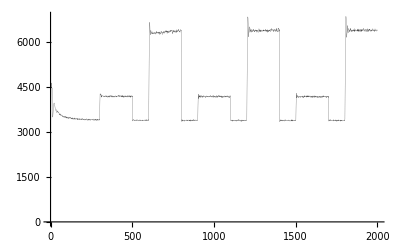

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.98,3819.55,5228.13,6245.51,6895.81,7191.77,7297.62,7235.07,7207.73,7034.23,6985.77,6939.89,6740.1,6485.41,6299.65,6103.5,5942.26,5914.65,5832.41,5803.05,5807.97,5923.93,6242.32,6293.47,6195.08,6180.,6037.25,5867.22,5660.19,5595.74,5669.33,5835.92,5829.09,5798.9,5867.75,5826.5,5797.66,5845.82,5926.87,5903.24,5818.84,5714.67,5496.49,5556.08,5522.27,5480.57,5488.79,5382.14,5311.39,5311.14,5297.77,5251.92,5215.03,5157.42,5152.61,5076.65,5074.41,4999.73,5014.79,4978.91,4972.04,4876.28,4961.58,4920.28,4883.42,4926.23,4890.13,4841.69,4778.24,4755.41,4766.83,4747.22,4716.41,4747.36,4707.03,4640.39,4663.84,4593.07,4695.29,4648.71,4606.79,4657.58,4629.62,4555.94,4526.97,4530.32,4493.5,4505.26,4541.48,4539.42,4507.33,4495.85,4528.95,4564.45,4603.91,4655.74,4696.37,4676.39,4657.58,4629.76,4618.41,4584.87,4580.4,4545.32,4577.24,4498.3,4502.22,4504.6,4424.39,4462.86,4495.86,4507.13,4504.11,4560.98,4555.36,4554.37,4539.5,4575.26,4629.16,4603.1,4623.79,4603.32,4532.55,4483.69,4541.08,4548.79,4627.46,4583.04,4553.73,4551.39,4645.22,4635.23,4564.7,4522.2,4519.08,4442.77,4402.55,4462.27,4510.62,4564.21,4523.55,4508.74,4561.42,4658.27,4745.95,4725.21,4689.05,4699.08,4708.58,4795.2,4775.08,4651.06,4685.,4755.43,4702.36,4622.58,4684.5,4643.55,4626.77,4649.06,4634.41,4646.41,4629.63,4641.75,4665.63,4777.22,4723.69,4793.08,4732.72,4666.39,4668.66,4688.36,4696.05,4692.58,4563.96,4557.94,4632.88,4725.71,4765.99,4804.74,4726.95,4683.36,4643.3,4633.2,4638.57,4571.29,4656.36,4629.13,4655.43,4633.57,4711.05,4715.47,4716.22,4730.23,4682.11,4725.7,4877.,4874.39,4856.64,4848.11,4969.45,4794.08,4760.82,4849.28,4900.97,4831.68,4818.56,4774.41,4768.03,4780.75,4859.28,4787.33,4738.99,4781.95,4707.39,4827.67,4731.65,4867.51,4935.37,5013.32,4983.91,4900.5,4807.34,4928.97,5050.26,5014.32,4891.08,4863.54,4902.66,4904.98,4917.59,4841.85,4755.19,4847.79,4854.49,4843.49,4929.97,4877.66,4911.17,4898.9,4882.74,4861.03,4857.4,4878.16,4960.89,4960.95,4977.31,4962.27,4865.88,4912.49,4918.88,4939.01,4953.74,4942.16,4898.83,4934.82,4989.86,5029.17,4919.23,4940.05,4972.36,4911.66,4811.28,4811.87,4840.83,4858.27,4859.45,4867.15,4889.25,4913.63,4869.92,4872.42,4843.08,4926.88,4992.71,5033.56,4998.29,4990.67,5039.13,5086.07,5171.31,5157.6,5113.9,5098.05,5100.36,5092.57,5095.88,5056.52,5060.85,4961.49,4880.38,4892.79,4826.65,4881.32,4846.84,4892.86,5020.27,4985.95,4990.5,5018.06,5014.57,5133.76,5173.65,5129.62,5044.71,5017.82,5055.42,5133.04,5135.21,5130.96,5163.28,5221.9,5179.33,5193.38,5171.56,5128.11,5149.85,5153.59,5113.22,4983.52,4979.69,4901.34,4951.81,5008.98,5119.56,5068.96,4995.49,4883.27,4839.89,4946.53,4996.,4960.3,4898.51,5010.,4959.41,5017.04,5142.53,5092.67,5040.37,5067.29,4981.43,4924.57,4949.56,4944.07,4949.65,4971.02,4950.43,4930.18,4988.69,5072.75,5084.78,4990.47,5037.58,5045.15,5129.48,5045.33,5026.16,5096.49,5176.51,5206.29,5181.35,5145.93,5218.29,5298.57,5188.68,5210.12,5243.48,5212.81,5079.57,5151.42,5117.63,5151.85,5157.54,5144.7,5105.13,5066.27,5138.73,5182.94,5249.8,5227.28,5236.01,5227.21,5120.51,5124.48,5192.93,5211.84,5113.59,4986.45,4945.6,4994.41,5041.86,5079.75,5128.82,5116.07,5114.01,5028.49,5103.36,5147.74,5226.44,5291.27,5255.02,5213.75,5219.3,5248.29,5291.74,5297.04,5322.16,5227.12,5191.74,5097.03,5058.97,5068.34,5099.73,5051.84,5033.52,5008.55,5103.76,5064.19,5081.99,5154.32,5187.95,5112.91,5194.9,5327.33,5385.54,5327.73,5250.99,5162.6,5186.34,5231.69,5239.58,5228.49,5242.86,5255.33,5240.55,5252.08,5303.06,5342.29,5401.09,5336.76,5353.84,5226.06,5217.66,5232.49,5243.39,5258.61,5241.45,5153.56,5153.68,5184.07,5193.32,5188.94,5228.63,5147.14,5234.03,5254.19,5288.05,5274.36,5283.7,5341.99,5347.53,5409.95,5496.19,5447.15,5437.99,5420.83,5396.6,5430.39,5413.96,5288.98,5245.56,5234.25,5245.21,5290.78,5290.47,5226.98,5251.93,5311.74,5394.77,5356.68,5371.14,5342.66,5298.01,5277.08,5351.38,5478.76,5492.92,5555.31,5426.5,5323.06,5330.17,5420.59,5393.03,5394.87,5283.93,5344.91,5386.02,5333.8,5390.12,5484.91,5484.94,5439.6,5410.64,5405.82,5336.65,5231.95,5257.12,5269.73,5271.21,5317.39,5354.33,5362.87,5274.47,5200.46,5135.17,5145.83,5236.65,5229.81,5374.6,5344.99,5260.97,5265.33,5296.9,5213.36,5156.75,5161.05,5201.04,5177.,5216.65,5165.58,5278.26,5382.86,5352.96,5261.74,5247.93,5260.94,5366.76,5469.58,5482.22,5486.99,5580.01,5617.24,5688.31,5659.73,5545.8,5431.47,5440.3,5466.63,5416.13,5422.36,5413.76,5465.81,5504.08,5477.51,5511.22,5425.26,5427.03,5433.43,5488.58,5439.38,5392.59,5481.13,5422.78,5520.53,5531.67,5394.05,5441.52,5502.13,5505.58,5545.19,5519.29,5356.74,5232.1,5271.55,5421.74,5546.69,5547.5,5462.88,5435.29,5547.89,5621.72,5555.97,5486.58,5302.81,5327.38,5188.74,5295.87,5408.49,5341.74,5385.14,5283.32,5298.99,5259.77,5301.01,5367.75,5416.24,5515.12,5540.76,5494.31,5454.76,5463.33,5561.81,5423.91,5368.04,5463.59,5573.19,5533.09,5470.99,5419.64,5481.45,5649.86,5731.72,5719.34,5621.72,5586.66,5571.18,5557.27,5682.14,5674.81,5673.9,5515.55,5511.62,5530.36,5466.21,5522.99,5579.66,5701.21,5718.45,5737.86,5525.87,5448.71,5477.14,5460.5,5463.16,5465.21,5456.7,5455.32,5529.04,5443.88,5474.09,5491.18,5511.38,5574.68,5541.24,5517.26,5440.2,5511.37,5592.09,5651.01,5539.13,5501.57,5512.58,5577.52,5564.95,5502.81,5485.85,5584.15,5720.85,5649.59,5556.25,5580.41,5568.61,5618.55,5583.16,5560.37,5534.94,5557.63,5559.93,5563.45,5565.45,5637.44,5559.55,5508.62,5500.05,5628.52,5564.13,5599.47,5560.14,5560.69,5574.42,5563.1,5581.62,5413.28,5433.17,5391.58,5470.39,5454.13,5558.78,5546.7,5535.54,5565.98,5461.78,5472.6,5546.78,5553.45,5508.26,5412.51,5509.34,5555.45,5507.33,5641.02,5626.07,5616.65,5560.45,5609.28,5663.28,5717.29,5828.54,5886.43,5829.16,5717.24,5713.73,5721.33,5685.5,5551.21,5589.79,5494.32,5668.44,5758.21,5789.87,5705.21,5673.39,5655.7,5633.55,5733.06,5817.8,5857.6,5896.89,5864.74,5770.82,5704.31,5645.02,5747.19,5686.77,5741.57,5752.91,5581.41,5471.8,5471.86,5542.79,5692.98,5736.8,5722.2,5626.16,5666.97,5656.85,5666.92,5715.9,5596.32,5598.46,5554.69,5588.44,5579.13,5668.21,5638.95,5638.72,5570.22,5507.12,5522.44,5609.72,5615.01,5594.35,5569.11,5564.03,5666.22,5787.59,5804.95,5673.79,5758.96,5886.4,5840.58,5789.53,5827.49,5799.46,5748.52,5785.01,5903.3,5817.19,5704.11,5675.32,5745.62,5786.72,5838.44,5821.91,5812.57,5867.54,5877.33,5713.12,5596.28,5464.64,5484.27,5550.51,5621.43,5809.06,5907.71,5906.94,5843.7,5678.37,5645.94,5652.87,5616.76,5720.56,5764.32,5603.46,5557.11,5619.56,5614.51,5606.88,5666.53,5564.69,5553.96,5457.99,5520.24,5541.15,5584.86,5586.39,5545.02,5474.7,5525.6,5553.67,5687.33,5679.87,5620.72,5683.41,5774.94,5792.17,5718.81,5566.75,5569.19,5482.44,5553.65,5609.4,5594.85,5594.15,5735.48,5784.68,5731.85,5746.77,5782.1,5801.78,5837.55,5891.61,5903.18,5842.64,5770.54,5646.66,5726.46,5893.85,5901.66,5869.66,5743.1,5727.04,5743.17,5738.78,5825.51,5787.91,5728.08,5673.43,5738.24,5773.57,5861.05,5976.3,5900.67,5879.04,5825.4,5918.97,5735.26,5669.48,5622.75,5645.2,5830.46,5788.18,5761.07,5711.82,5650.58,5709.48,5807.22,5699.01,5585.86,5678.18,5708.62,5811.09,5888.23,5855.57,5861.59,5839.74,5843.29,5936.04,5941.99,5831.16,5883.3,5852.23,5962.31,5916.53,5888.26,5842.13,5892.29,6042.75,6046.22,5961.66,5938.4,5895.52,5960.18,5864.18,5689.72,5603.3,5709.28,5761.51,5742.63,5764.92,5780.49,5875.75,5796.25,5763.32,5811.38,5807.43,5711.76,5572.13,5625.88,5635.89,5592.44,5735.3,5712.77,5716.93,5684.47,5809.58,5833.13,5887.74,5839.16,5894.83,5953.44,6036.16,5966.28,5934.23,5932.86,5892.95,5848.99,5886.7,5809.34,5812.09,5922.47,6012.98,6122.12,6041.93,5936.61,6010.22,5920.81,5888.85,5827.9,5743.87,5806.9,5969.28,6044.19,6028.79,5864.67,5692.52,5789.26,5914.29,5825.37,5759.94,5826.76,5954.14,5896.35,5801.84,5676.66,5669.06,5683.21,5840.22,5883.03,5809.59,5752.92,5661.31,5639.97,5674.31,5778.51,5755.59,5776.,5673.24,5717.11,5647.54,5680.17,5780.78,5937.29,5890.29,5885.59,5879.4,5931.16,6015.15,6081.63,6105.45,6029.13,5890.43,5885.18,5919.95,6045.3,5953.92,5910.69,5940.88,5982.09,5826.02,5818.28,5925.89,5940.04,5983.5,5940.85,5914.64,5796.73,5745.85,5736.11,5745.6,5899.2,5929.68,5994.58,5932.61,5936.42,5921.71,5898.14,5861.88,5764.55,5780.18,5693.84,5782.47,5833.38,5841.44,5804.77,5802.8,5763.16,5644.1,5526.74,5526.42,5523.65,5626.14,5804.48,5864.49,5886.07,5772.,5728.05,5699.31,5788.37,5885.28,5982.47,6035.2,5954.1,5960.7,5876.42,5909.74,6002.83,6210.03,6224.13,6180.58,6208.99,6059.68,5999.19,5890.33,5939.96,6025.64,6030.28,6049.29,6059.39,5931.75,5931.81,5934.07,6077.68,6102.65,6081.24,5892.25,5924.87,5883.94,5904.2,5866.9,5848.49,5843.72,5893.94,5927.77,5893.86,5914.72,5875.11,5992.15,6029.84,5975.51,5806.72,5849.85,5966.71,6131.64,5922.81,5823.36,5968.53,6026.12,5871.52,5862.93,5788.13,5901.3,5912.35,6038.36,5989.12,6007.1,6042.09,5975.9,6104.81,6109.61,6000.1,5939.91,5943.82,5866.4,5896.95,5917.55,5955.86,6054.48,6091.35,6096.3,6168.55,6128.99,6100.85,5898.15,5802.53,5782.25,5792.9,5875.34,5938.26,5762.15,5723.27,5864.45,5822.91,5844.72,5917.8,5951.23,5976.8,5904.64,5796.5,5763.6,5777.2,5953.57,5842.97,5892.72,5861.12,5955.08,6012.52,5993.25,5938.04,5826.26,5780.74,5962.93,6027.61,5984.18,5804.75,5805.23,5804.07,5730.47,5789.49,5813.6,5951.88,6033.02,6053.7,5965.5,5961.98,5877.5,5836.1,5751.52,5765.65,5903.74,5965.79,5869.25,5937.79,5951.27,5862.27,5778.93,5746.97,5851.,5895.49,5851.15,5942.32,6028.16,5896.99,5856.26,5915.37,5955.53,5853.31,5830.96,5802.41,5846.65,5934.,5936.01,6024.87,5981.51,6091.93,6108.34,6187.08,6123.65,6032.27,6063.2,6028.9,5976.6,6033.65,6024.,5986.75,6071.68,6068.86,6077.3,6042.23,5973.77,5988.03,6054.61,6112.57,6111.38,6024.81,5942.07,5793.08,5833.26,5904.39,5873.14,5959.06,6055.28,6174.92,6157.1,6079.81,5937.31,5782.97,5768.13,5915.03,5940.28,6010.71,5911.52,5889.29,5900.32,6099.08,6172.17,6098.06,6037.17,6088.88,6058.85,6144.44,6193.,6061.73,6066.7,6193.96,6220.3,6284.68,6201.58,6057.04,6045.,6059.77,6155.35,6204.3,6160.22,6116.95,5941.74,5775.89,5854.09,5993.02,6060.53,6118.23,6224.35,6301.35,6281.37,6195.94,6154.28,6177.13,6157.33,6148.4,6145.66,6145.31,6156.91,6086.35,6031.06,6010.8,6016.4,6014.34,5820.07,5827.46,5952.65,6085.27,6099.83,6132.23,6103.73,6087.65,6184.81,6220.62,6138.25,6057.63,6157.93,6228.24,6151.18,6047.56,5921.98,6050.08,6148.08,6102.41,6034.48,6110.32,6007.56,5899.52,5925.8,6002.99,6060.85,6064.49,5941.87,5966.54,6056.92,6117.81,6088.18,5969.89,5904.53,5981.6,6091.79,6079.65,6187.6,6255.92,6284.81,6243.06,6066.78,6058.3,5939.5,5921.56,5953.6,6053.4,6135.48,6247.82,6222.11,6176.18,6015.97,5833.24,5979.55,6083.65,6074.08,6007.07,6043.97,6023.17,5971.99,5922.93,6039.3,6155.,6164.19,6233.75,6224.23,6018.98,5982.07,6028.73,6045.93,6121.41,6171.44,6265.22,6196.22,6072.52,6058.28,6008.55,6169.15,6277.64,6214.82,6190.14,6071.57,6107.27,6119.71,6063.88,6140.33,6165.66,6115.77,6210.13,6093.17,6134.92,6158.61,6058.61,6030.26,6122.66,6107.01,6092.07,6065.53,6032.12,6078.15,6205.4,6148.64,6030.53,6007.62,5958.19,5863.65,5858.86,5925.97,5941.,6054.07,6239.,6282.36,6221.61,6126.91,6038.19,5982.35,6094.07,6072.53,6045.46,6038.32,5968.08,5963.09,5932.93,5995.28,6007.06,6025.45,6036.32,6076.36,5923.42,6006.71,6146.87,6148.17,6099.1,6143.08,6195.6,6163.83,5980.52,6002.88,5903.63,5908.02,5959.97,6019.31,6022.2,6098.9,6215.69,6090.32,6030.72,5888.78,5954.8,5984.89,5946.22,5950.36,5941.67,5951.41,6016.57,6093.05,6191.64,6242.03,6053.34,5951.24,5882.76,5962.79,6037.16,6052.27,6256.41,6405.41,6541.53,6418.81,6411.47,6361.86,6346.13,6233.14,6226.11,6273.87,6344.36,6395.85,6382.75,6304.39,6279.09,6290.6,6311.74,6106.31,6144.82,6284.18,6181.68,6092.51,6196.03,6231.02,6181.99,6162.19,6178.61,6229.78,6262.31,6118.92,6114.92,6129.73,6186.11,6146.64,6143.11,6110.52,6020.13,6091.4,6084.32,6123.02,6122.97,6191.43,6281.26,6235.51,6298.95,6256.39,6296.02,6239.5,6273.87,6206.99,6263.1,6252.58,6297.02,6313.72,6239.64,6291.7,6486.42,6503.74,6408.34,6324.92,6082.87,5980.24,5919.27,6054.21,6096.,6118.82,6182.93,6276.33,6367.44,6380.9,6265.15,6232.07,6070.17,6025.47,6056.2,5976.65,6032.28,5969.5,6015.23,6059.03,6026.77,6070.14,6119.25,6021.43,6046.61,6071.5,5998.62,5969.41,5998.7,6088.21,6055.79,6075.04,6168.59,6147.59,6187.27,6097.25,6214.59,6082.72,5991.22,6071.71,6105.42,6018.72,5995.23,5939.01,5782.68,5926.36,6013.04,6173.29,6149.67,6088.42,6057.12,6128.53,6234.79,6258.09,6226.07,6211.56,6188.2,6160.05,6190.03,6139.52,6205.96,6282.33,6295.58,6376.24,6197.09,6168.28,6095.18,6103.26,6131.33,6196.82,6200.13,6280.33,6318.65,6275.6,6334.9,6271.03,6301.18,6361.88,6316.47,6200.24,5994.07,6187.7,6464.59,6616.5,6494.46,6352.37,6262.64,6195.45,6299.27,6333.46,6458.25,6480.84,6358.94,6265.82,6296.37,6244.36,6304.66,6226.27,6265.17,6312.63,6093.95,6052.31,6011.58,5931.33,5920.9,6034.15,6061.88,6037.95,6020.94,6060.93,6087.71,6129.21,6173.2,6371.2,6292.85,6240.19,6107.18,6185.28,6168.19,6153.41,6163.8,6172.59,6170.53,6121.73,6173.07,6177.07,6184.75,6185.07,6119.89,6147.62,6117.59,6106.53,6189.66,6192.46,6257.43,6171.27,6080.8,6124.6,6115.71,6199.98,6134.84,6160.31,6201.65,6289.54,6247.28,6252.59,6206.78,6082.62,5962.14,5922.39,6044.06,6071.95,6111.22,6171.37,6153.46,6054.13,6144.27,6137.9,6129.03,6159.06,6228.62,6365.86,6338.04,6244.82,6205.97,6270.06,6397.25,6412.94,6190.98,6091.53,6219.06,6288.03,6292.21,6279.15,6407.26,6387.55,6385.63,6423.57,6415.2,6315.78,6177.85,6182.41,6145.84,6141.6,6190.89,6216.85,6402.7,6331.98,6316.92,6334.42,6298.8,6284.,6338.24,6287.91,6282.78,6340.58,6350.2,6417.67,6342.73,6321.61,6256.32,6251.25,6344.44,6487.18,6511.66,6452.37,6300.75,6207.29,6282.32,6402.02,6396.25,6468.94,6378.98,6313.01,6189.73,6178.86,6158.25,6173.88,6250.54,6200.97,6279.42,6334.77,6412.15,6427.2,6402.22,6513.5,6383.98,6425.97,6466.87,6355.71,6266.01,6312.58,6192.96,6185.07,6268.56,6338.56,6374.32,6525.37,6410.37,6251.53,6224.95,6168.19,6129.89,6168.95,6224.55,6314.02,6411.54,6417.39,6451.79,6457.36,6512.49,6528.02,6401.6,6394.81,6288.16,6281.53,6355.55,6309.69,6364.01,6379.41,6391.33,6382.53,6428.16,6275.54,6161.29,6141.62,6111.15,6132.03,6297.83,6288.44,6422.58,6476.84,6585.17,6488.99,6331.89,6329.13,6264.89,6400.05,6498.77,6545.81,6352.85,6323.71,6325.78,6305.46,6306.64,6492.38,6467.26,6507.81,6576.71,6650.61,6671.6,6512.41,6474.6,6324.16,6367.75,6489.61,6316.47,6306.77,6350.18,6398.91,6437.1,6429.87,6478.89,6433.52,6298.3,6137.17,6118.69,6237.,6374.79,6431.64,6464.36,6409.35,6422.99,6413.23,6365.71,6410.47,6485.14,6477.66,6521.46,6367.5,6348.54,6275.19,6223.95,6223.82,6133.24,6164.31,6119.96,6216.87,6278.23,6175.8,6246.72,6152.38,6192.67,6362.4,6457.9,6418.1,6349.91,6292.97,6261.12,6292.89,6285.75,6251.8,6272.63,6272.26,6363.73,6296.24,6319.8,6369.27,6433.43,6328.07,6286.79,6226.7,6147.66,6174.87,6163.58,6290.38,6466.73,6567.2,6486.88,6280.83,6356.58,6288.43,6300.27,6193.04,6113.87,6197.19,6263.25,6403.17,6384.08,6262.35,6329.7,6331.69,6337.65,6473.73,6415.65,6414.13,6349.25,6231.23,6323.9,6312.76,6278.59,6243.42,6365.88,6361.69,6245.23,6141.6,6128.94,6175.99,6206.92,6197.64,6249.55,6254.48,6199.32,6384.63,6284.54,6259.75,6304.01,6221.2,6376.86,6472.22,6538.67,6454.75,6347.17,6097.04,6107.84,6215.98,6352.31,6449.26,6339.4,6188.3,6154.17,6239.7,6162.09,6133.19,6115.47,6048.49,6189.73,6145.5,6161.88,6254.41,6267.41,6189.06,6212.33,6232.57,6317.42,6199.23,6211.59,6200.26,6273.69,6371.67,6335.27,6487.5,6489.16,6483.98,6384.63,6381.86,6256.55,6272.76,6343.91,6271.6,6301.74,6312.81,6407.06,6365.77,6310.44,6311.76,6153.4,6233.33,6296.2,6392.53,6353.02,6410.29,6417.28,6473.39,6468.37,6450.1,6362.32,6325.45,6353.54,6390.89,6347.56,6397.94,6348.46,6313.21,6180.79,6155.67,6146.68,6291.52,6319.97,6432.71,6457.82,6458.73,6460.39,6408.51,6377.28,6250.65,6161.49,6230.96,6289.2,6338.18,6442.29,6472.68,6440.22,6288.02,6166.14,6191.28,6133.41,6080.05,6211.33,6288.73,6376.55,6380.1,6218.34,6127.53,6254.42,6297.4,6357.55,6331.54,6303.77,6412.47,6503.77,6498.91,6477.3,6451.74,6416.45,6330.69,6282.65,6285.73},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[« 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.13,3262.75,3788.06,3944.88,4008.17,4047.72,4137.85,4275.44,4301.04,4427.44,4618.68,4675.94,4723.99,4822.7,4825.83,4852.71,4861.77,4894.34,4995.,5007.46,4931.42,5110.27,5216.11,5211.85,5226.93,5155.76,5268.63,5279.09,5353.37,5302.44,5327.19,5373.91,5454.5,5495.08,5434.14,5370.55,5436.03,5438.88,5490.53,5462.04,5499.88,5549.1,5532.28,5506.99,5533.16,5633.09,5610.61,5554.5,5565.74,5585.1,5700.14,5752.02,5710.03,5708.28,5750.25,5751.24,5726.67,5696.59,5878.98,5931.35,5900.63,5794.2,5969.61,6024.34,5860.35,5777.78,5892.26,5760.17,5740.22,5845.41,6057.66,6062.79,6102.58,6029.3,5866.84,6101.82,6059.81,6008.85,5967.12,5935.36,6024.86,6081.2,6100.81,6065.87,6031.64,5896.86,5864.47,5924.33,5965.38,6002.16,6044.11,5983.71,5783.19,5862.65,5981.16,6060.28,6018.77,6000.32,6041.37,6046.54,6014.82,5986.1,6034.06,6016.6,6097.89,6118.71,6051.98,6041.16,6086.77,6229.8,6325.61,6292.03,6265.36,6157.07,6108.88,6121.65,6235.72,6350.55,6282.04,6246.23,6220.83,6083.91,6023.75,6085.49,6066.62,6190.58,6384.47,6518.71,6469.78,6254.71,6234.45,6318.25,6225.92,6158.65,6281.95,6390.8,6377.6,6514.03,6439.87,6366.38,6413.49,6396.92,6270.22,6215.31,6218.86,6117.78,6231.97,6203.85,6104.58,6162.4,6105.15,6096.96,6061.1,6123.21,6128.59,6252.35,6263.22,6270.28,6315.79,6263.91,6277.2,6116.56,6082.5,6076.45,6064.73,6067.05,6178.45,6239.56,6245.42,6210.16,6239.24,6291.87,6246.33,6124.75,6206.23,6256.09,6121.84,6102.83,6059.44,6065.04,6065.8,6033.28,5976.53,6040.89,6063.63,6049.78,6139.95,6157.78,6106.28,5985.14,6045.37,6119.28,6250.81,6181.,6308.99,6347.75,6251.75,6217.2,6048.65,6046.76,6052.98,6137.55,6088.81,5982.89,6055.52,5983.4,6005.8,6026.08,6086.65,6123.47,6145.66,6113.66,5962.25,5887.7,5879.29,5918.56,5927.33,5981.56,5974.29,6154.14,6032.86,6080.53,6083.99,6100.46,5944.36,5986.48,5946.91,5979.58,6085.47,6089.07,6074.17,6115.14,6124.75,6144.57,6106.39,6040.47,5924.57,6049.13,6054.57,5995.37,5800.33,5770.79,5746.85,5778.23,6115.91,5923.54,5929.66,5811.92,5852.13,5867.02,5921.66,6017.79,6046.36,5997.,5952.16,5861.51,6021.91,6128.59,6249.85,6108.33,6079.53,6153.8,6447.41,6311.46,6149.57,6131.47,6204.44,6126.95,5982.31,6045.12,6048.24,5949.48,6116.87,6145.92,6032.46,6095.44,6175.61,6010.64,6024.13,6204.77,6157.39,6314.8,6353.23,6261.69,6129.06,6147.18,6295.33,6346.8,6162.97,6019.51,6059.84,5998.03,6025.2,6157.42,6177.67,6215.18,6310.95,6307.58,6279.63,6334.88,6208.36,6159.18,6046.38,6020.86,6075.75,6252.77,6244.04,6221.63,6079.33,6077.95,6257.17,6332.43,6335.42,6257.71,6259.23,6098.4,6149.76,6303.68,6228.05,6125.24,6055.28,6034.23,5979.18,6036.54,6001.52,6053.85,6058.46,5943.72,6031.15,6079.1,6002.19,5890.31,5787.76,5807.21,5970.63,6051.97,6051.84,6068.74,6098.32,6113.59,6214.97,6203.59,6052.02,6237.23,6322.06,6224.87,6252.56,6139.64,6148.37,6237.72,6203.11,6109.7,6099.86,6137.28,6239.88,6378.37,6290.63,6152.38,6070.41,6161.73,6227.04,6174.1,6340.24,6241.04,6185.61,6180.22,6160.09,6201.13,6332.01,6277.64,6246.43,6373.57,6316.87,6226.41,6239.47,6235.57,6093.4,6155.67,6185.3,6248.29,6129.35,6148.85,6116.42,6171.45,6053.25,6050.29,6225.21,6150.2,6183.9,5967.45,5948.41,6043.29,6123.28,6083.84,6014.95,6102.5,6081.35,6162.42,6226.14,6235.31,6145.03,6109.11,6063.01,6040.14,6045.95,5986.88,5984.59,6037.48,5990.17,5891.94,5922.67,5934.52,5913.84,5989.24,6063.09,6075.81,5982.96,6020.65,5985.76,6016.34,5994.62,5877.98,6009.66,5984.98,6001.48,6034.51,6093.44,6181.6,6249.67,6226.76,6120.83,6101.42,6142.53,6108.76,6161.59,6183.76,6157.03,6048.7,6033.19,6015.69,6146.09,6181.64,6258.93,6053.65,6001.98,6078.58,6187.52,6294.73,6471.03,6406.19,6208.96,6233.85,6171.5,6309.47,6364.93,6303.27,6333.9,6301.6,6105.41,6175.9,6195.26,6287.69,6516.55,6403.32,6278.8,6393.24,6250.55,6261.33,6358.1,6346.76,6228.65,6298.14,6304.89,6367.69,6209.02,6252.9,6194.03,6266.67,6380.24,6396.85,6350.05,6232.23,6391.49,6418.83,6338.6,6279.33,6106.37,6096.13,6187.27,6265.68,6296.3,6488.47,6442.46,6360.27,6269.33,6180.32,6338.81,6355.5,6277.61,6281.98,6220.47,6219.77,6344.89,6416.24,6363.61,6424.35,6379.95,6438.72,6361.96,6328.27,6359.32,6327.25,6199.26,6162.81,6164.42,6060.65,6185.3,6064.83,6042.53,6068.46,6187.3,6213.85,6146.93,6182.86,6189.31,6331.1,6355.43,6385.69,6248.45,6382.46,6259.88,6277.1,6271.99,6222.3,6102.25,6213.39,6243.35,6177.74,6146.72,6012.73,5872.2,6072.61,6198.31,6271.25,6319.1,6394.14,6346.37,6228.19,6210.58,6178.17,6266.33,6398.55,6208.31,6044.58,5959.19,6020.82,6200.9,6271.39,6168.51,6093.43,6088.69,6058.17,6077.79,6043.37,6147.58,6149.86,6148.04,6010.01,5974.1,5907.,6008.12,6255.32,6367.3,6270.13,6136.02,6156.42,6059.93,6023.95,6049.78,6196.63,6074.86,6059.66,6249.02,6285.38,6246.64,6225.55,6204.04,6206.53,6107.64,6100.6,6162.31,6236.4,6157.56,6218.31,6096.06,6125.13,6235.87,6212.47,6160.45,6207.82,6230.86,6208.04,6110.18,6055.48,6087.97,6114.03,6064.77,5993.15,5973.73,6154.3,6084.76,6269.35,6351.01,6255.99,6158.31,6223.3,6117.,6116.67,6035.83,6046.42,5952.31,6152.14,6165.64,6195.,6277.05,6190.34,6239.97,6171.7,6020.99,6019.22,6129.99,6213.31,6077.28,5931.18,5942.61,5935.,6046.29,6258.01,6167.27,6080.22,5919.08,5954.51,5999.43,5976.05,5821.03,5907.41,5999.96,6139.23,6187.15,6201.44,6224.16,6191.52,6072.52,6089.62,6143.03,6062.65,6039.94,6096.65,6133.14,6105.42,6017.42,6127.94,6192.82,6248.77,6287.05,6188.52,6062.18,6089.78,6074.1,6072.27,6022.09,5941.37,6006.52,6023.23,5937.26,5915.66,5917.28,5956.69,5881.64,5913.25,5759.5,5863.16,6037.35,5980.14,5974.09,6073.32,6146.,6101.98,6117.86,6082.2,6087.77,6084.45,6186.48,6291.84,6392.71,6455.25,6469.,6384.39,6411.51,6318.95,6351.87,6335.18,6369.35,6261.6,6404.72,6312.01,6184.31,6174.64,6158.27,6249.81,6378.94,6397.97,6428.23,6356.4,6466.29,6390.16,6363.35,6292.44,6312.91,6408.96,6362.1,6349.9,6293.53,6180.67,6128.18,6192.51,6138.98,6369.46,6391.4,6552.57,6403.22,6306.46,6290.3,6193.54,6294.62,6396.57,6221.67,6179.85,6238.61,6291.84,6417.14,6301.46,6042.61,6125.01,6287.36,6482.91,6519.04,6421.66,6419.,6347.12,6416.07,6503.26,6476.84,6437.79,6345.19,6381.36,6430.43,6368.03,6495.6,6483.47,6457.9,6471.41,6344.52,6239.85,6504.71,6516.11,6517.91,6438.9,6348.19,6459.91,6293.75,6281.08,6427.41,6463.26,6346.86,6349.3,6300.06,6231.25,6273.63,6270.82,6325.43,6398.85,6337.56,6369.73,6407.87,6359.46,6319.14,6203.65,6218.32,6322.01,6190.05,6260.02,6215.79,6303.13,6378.03,6301.01,6249.12,6262.52,6174.45,6149.12,6239.89,6228.65,6286.35,6260.38,6375.94,6277.79,6252.45,6308.21,6211.98,6270.38,6232.39,6373.97,6407.49,6486.04,6451.02,6419.08,6219.,6256.88,6236.38,6284.03,6377.01,6318.75,6289.45,6382.61,6368.05,6248.43,6066.05,6158.62,6176.5,6312.49,6281.29,6347.1,6228.37,6096.38,6227.77,6380.54,6260.17,6257.5,6370.73,6416.23,6331.25,6308.85,6419.53,6388.66,6394.89,6286.09,6111.48,6148.84,6439.48,6471.25,6400.58,6301.37,6266.21,6159.97,6220.18,6317.11,6319.42,6203.89,6196.42,6384.33,6303.19,6357.2,6259.72,6223.59,6205.08,6245.59,6305.6,6299.16,6188.32,6391.81,6463.09,6563.42,6575.89,6492.96,6303.08,6244.45,6314.51,6348.5,6264.68,6340.92,6312.5,6275.19,6245.73,6424.18,6477.35,6437.64,6351.67,6185.73,6083.05,6179.84,6248.71,6291.24,6338.56,6284.15,6388.58,6391.64,6399.06,6456.75,6384.45,6271.8,6267.85,6203.37,6101.37,6161.78,6337.14,6315.22,6213.03,6209.,6277.31,6194.47,6213.99,6361.02,6389.25,6268.75,6286.48,6412.52,6393.46,6265.4,6235.18,6243.31,6182.63,6261.72,6304.66,6319.24,6422.05,6468.56,6253.32,6189.34,6228.91,6268.62,6301.4,6272.58,6272.08,6147.7,6271.44,6303.74,6293.48,6313.44,6254.98,6150.7,6225.69,6188.88,6175.52,6065.73,6037.5,6081.82,6157.56,6204.34,6203.95,6215.48,6166.35,6153.81,6151.1,6111.19,6155.35,6228.44,6085.4,6266.33,6286.25,6254.06,6138.49,6029.01,6092.73,6114.01,6028.8,6072.33,6080.46,6063.33,6107.86,6253.02,6173.81,6168.58,6282.35,6437.87,6270.61,6166.02,6152.07,6157.87,6024.94,6159.6,6318.98,6232.97,6239.27,6227.89,6199.94,6154.5,5997.31,6076.89,6044.5,6068.22,6111.69,6153.66,6147.98,6141.47,6118.75,6132.1,6169.62,6444.86,6353.6,6224.88,6006.21,6107.55,6232.63,6334.96,6358.25,6144.23,6258.79,6302.34,6291.31,6356.68,6398.65,6332.06,6399.16,6298.89,6340.65,6202.31,6112.31,6269.91,6288.71,6245.94,6263.74,6304.7,6233.92,6188.66,6251.72,6062.78,6107.77,6256.8,6318.91,6289.1,6241.85,6200.3,6181.31,6110.23,6133.98,6178.48,6238.02,6136.53,6080.72,6048.14,6242.08,6294.2,6308.52,6315.46,6346.61,6347.1,6292.62,6271.88,6165.6,6146.58,6239.51,6192.61,6192.35,6177.81,6273.76,6276.27,6174.29,6255.26,6114.84,6051.82,6137.91,6222.16,6215.61,6176.62,6168.92,6060.2,6043.78,6079.01,6110.98,6192.6,6325.11,6267.99,6033.73,6019.99,6077.12,6148.19,6218.52,6189.31,6121.31,6212.9,6054.33,6075.8,6056.69,6186.95,6233.46,6095.44,6188.26,6133.85,5999.66,6042.16,6246.25,6097.1,6135.78,6129.75,6131.18,6265.62,6294.13,6114.04,6091.26,6175.56,6213.21,6408.27,6443.65,6288.77,6277.85,6242.68,6146.74,6239.14,6266.85,6167.94,6152.34,6152.58,6183.61,6232.97,6257.27,6328.4,6257.07,6162.47,6079.34,6135.72,6239.53,6264.13,6334.15,6420.87,6316.08,6322.96,6319.07,6392.84,6322.29,6236.11,6288.64,6203.75,6226.55,6257.25,6266.9,6171.72,6260.73,6383.51,6434.08,6383.5,6281.11,6200.78,6102.01,6201.68,6149.23,6175.42,6139.15,6048.42,6166.81,6263.03,6361.53,6156.55,5978.4,6116.54,6168.51,6068.78,6134.85,6106.7,6203.88,6281.92,6205.9,6099.22,6128.93,6145.09,6241.53,6266.66,6229.44,6139.61,6079.09,6050.55,6105.21,6146.59,6310.16,6179.3,6181.42,6259.23,6283.05,6284.75,6272.94,6258.91,6210.32,6241.41,6238.87,6244.06,6201.28,6363.35,6461.44,6404.11,6114.95,6091.51,6267.94,6267.76,6178.58,6112.82,6005.2,6067.49,6136.89,6235.89,6302.82,6178.97,6138.82,6026.07,6023.16,5904.15,6041.65,6286.04,6336.56,6245.2,5990.46,6036.27,6156.12,6299.92,6147.44,6001.,5923.61,5992.62,6196.55,6210.39,6207.57,6040.87,6124.6,6125.92,6171.86,6208.84,6356.2,6335.69,6199.42,6065.78,6205.59,6307.69,6354.33,6195.33,6133.61,6060.78,6131.3,6270.3,6387.83,6398.72,6242.41,6449.01,6304.43,6146.9,6022.49,6130.93,6341.54,6371.99,6421.81,6407.05,6267.05,6416.08,6303.31,6288.85,6378.01,6362.76,6437.05,6351.38,6414.87,6413.19,6258.91,6200.56,6239.34,6170.51,6359.67,6460.02,6354.36,6200.97,6180.57,6304.79,6413.99,6425.56,6431.48,6319.91,6047.5,6145.65,6308.16,6348.77,6174.68,6185.95,6119.86,6304.01,6285.03,6221.66,6082.33,6125.27,6198.46,6351.31,6177.92,6085.67,6101.16,6203.38,6216.96,6371.83,6186.07,6149.01,6111.78,6168.47,6039.32,6079.21,6056.34,6060.02,6053.9,6011.37,6085.9,6058.94,6235.85,6268.2,6188.35,6051.23,6062.07,6027.07,6097.66,6148.,6096.82,5945.53,5848.71,5982.4,6013.53,6101.08,6078.32,5925.13,5925.83,6083.45,6067.96,6130.97,6100.1,5930.48,5817.54,5868.8,5929.67,6115.11,6135.12,6029.75,5946.7,6091.94,6112.02,6248.79,6304.98,6081.45,6219.68,6153.5,6135.,6032.62,5939.91,5950.47,5975.78,6079.45,6028.81,6025.36,6108.46,6168.73,6056.18,6117.09,6062.61,5930.04,6046.25,6119.97,6114.3,6030.85,5990.39,6020.01,5970.58,6061.15,6025.08,5963.35,6010.44,6029.59,6187.87,6058.66,5919.77,5831.2,6017.08,6142.9,6205.5,6078.24,5934.63,5983.32,6061.9,6102.79,5995.23,6113.59,6179.12,6210.99,6238.65,6150.47,6143.03,6035.26,6025.55,5849.56,5899.26,6129.67,6236.13,6146.13,6205.69,6091.04,6190.74,6346.53,6280.28,6199.89,6253.33,6179.02,6294.22,6353.48,6396.85,6284.62,6322.94,6333.56,6348.15,6250.95,6191.81,6366.6,6484.37,6466.99,6413.27,6431.57,6397.33,6273.3,6203.53,6295.06,6264.22,6341.03,6100.58,6042.76,6092.6,6192.73,6235.95,6107.51,6150.84,6212.1,6152.95,6145.66,6101.81,6101.1,6128.37,6269.35,6222.54,6333.21,6329.99,6205.69,6246.16,6158.01,6072.28,6100.47,6271.25,6242.43,6264.51,6483.08,6366.47,6484.97,6388.13,6430.1,6291.37,6123.61,6272.9,6095.94,6240.99,6406.25,6479.71,6580.3,6281.04,6383.24,6351.11,6261.02,6239.52,6305.12,6300.66,6293.37,6362.23,6309.4,6203.59,6124.31,6077.93,6100.22,6204.59,6158.59,6080.03,6194.1,6216.37,6101.31,6182.82,6286.53,6397.12,6407.79,6210.53,6187.77,6356.73,6406.78,6280.65,6249.54,6147.11,6279.14,6236.28,6257.52,6153.15,6030.61,6126.47,6152.15,6241.32,6365.11,6280.07,6110.79,6055.39,6042.34,6161.11,6088.33,6188.19,6177.58,6135.65,6105.12,6246.25,6182.83,6373.63,6275.23,6160.88,6163.36,6278.87,6288.18,6135.93,6188.,6234.6,6374.06,6271.68,6196.59,6240.75,6194.37,6146.45,6226.97,6240.33,6114.57,5994.35,5884.6,6011.62,6329.46,6146.57,6099.96,5955.76,5956.9,6060.68,5875.99,5983.11,5944.75,5994.08,5964.36,6027.19,6036.77,6096.77,6095.17,6182.58,6261.99,6091.16,6183.73,6256.23,6240.5,6204.57,6295.44,6364.7,6218.02,6090.11,6072.34,6052.34,6228.66,6243.06,6110.91,6158.95,6248.66,6176.1,6218.01,6151.4,6163.75,6105.19,6022.17,6070.68,6121.76,6118.58,6136.98,6032.15,5922.51,5963.88,6016.81,6122.14,6247.84,6151.8,6117.8,6051.79,5969.62,5863.69,5951.47,5995.14,6081.16,6387.78,6260.16,6186.55,6221.15,6229.18,6188.52,6278.1,6332.88,6327.61,6283.15,6209.78,6309.92,6334.77,6330.34,6198.67,6377.94,6354.36,6258.19,6073.69,6197.41,6222.82,6242.4,6228.42,6252.97,6264.65,6307.02,6182.62,6052.66,6132.8,6200.87,6236.53,6304.01,6465.6,6463.06,6300.5,6202.45,6050.15,6103.9,6123.24,6123.44,6174.11,6205.86,6198.69,6303.58,6150.58,6151.47,6092.7,6236.3,6287.98,6196.08,6203.68,6219.1,6104.05,6035.42,6091.72,6290.33,6317.65,6258.08,6110.15,6136.09,6189.59,6094.16,6275.23,6230.72,6385.96,6224.66,6357.48,6505.77,6422.94,6342.68,6328.52,6380.9,6268.71,6145.21,6115.74,6055.03,5995.01,6174.67,6223.77,6191.96,6225.3,6062.44,6072.17,6038.19,6157.02,6202.97,6295.83,6299.5,6288.87,6262.21,6281.2,6304.4,6274.26,6241.74,6331.85,6301.82,6313.75,6295.3,6241.49,6166.74,6281.17,6262.98,6309.09,6320.83,6514.59,6472.75,6410.56,6291.47,6282.4,6386.73,6528.94,6547.07,6334.95,6337.88,6415.34,6166.78,6235.55,6207.99,6344.05,6333.44,6245.27,6220.36,6219.86,6044.89,6235.78,6268.71,6214.24,6240.37,6181.69,6177.75,6247.7,6231.8,6621.84,6707.31,6536.33,6310.02,6214.84,6327.06,6371.77,6373.77,6510.68,6553.29,6462.99,6502.96,6450.02,6512.92,6494.53,6343.28,6576.92,6461.91,6429.12,6320.58,6457.03,6501.41,6359.48,6409.27,6438.81,6383.88,6313.85,6192.76,6321.43,6306.54,6217.69,6226.81,6209.76,6095.53,6120.03,6261.6,6177.63,6080.05,6050.24,6179.59,6251.33,6266.36,6181.45,6198.25,6289.66,6211.35,6157.3,6268.38,6208.85,6383.18,6292.1,6160.36,6194.85,6058.7,6080.77,6064.46,6128.7,6306.18,6449.1,6478.16,6402.52,6505.65,6482.6,6457.95,6407.52,6398.54,6260.49,6170.91,6205.67,6318.76,6310.33,6295.02,6257.27,6197.58,6160.71,6357.29,6536.56,6690.34,6661.15,6404.06,6302.38,6462.22,6340.69,6271.93,6196.32,6175.52,6240.94,6202.97,6073.36,6068.76,6269.58,6356.14,6366.36,6340.41,6402.95,6257.7,6162.62,6193.63,6286.73,6144.06,6068.12,6103.82,6148.96,6114.62,6049.8,6133.12,6292.3,6238.09,6163.52,6209.3,6220.65,6224.95,6107.29,5996.02,6002.57,6091.87,6115.64,6108.43,6120.63,6060.7,6156.78,6177.82,6035.22,6102.89,6277.88,6318.46,6363.73,6221.02,6105.99,6175.21,6078.39,6123.72,6160.84,6158.98,6169.16,6124.6,6236.23,6280.83,6238.97,6284.14,6207.08,6155.54,6238.93,6086.28,6027.39,6213.82,5938.37,6012.83,6319.3,6326.37,6309.01,6275.32,6200.33,6167.19,6105.6,6083.79,6219.1,6321.43,6484.69,6397.,6256.32,6235.33,6267.09,6266.38,6297.14,6202.56,6325.66,6280.75,6229.77,6050.59,6148.91,6164.92,6250.22,6349.7,6272.74,6228.53,6211.95,6258.57,6309.06,6186.54,6257.26,6159.18,6182.85,6035.02,6057.57,6134.9,5995.09,6145.25,6188.78,6156.17,6078.53,6116.8,6219.05,6350.58,6231.29,6331.42,6271.57,6248.09,6320.8,6471.06,6384.06,6368.42,6467.01,6451.58,6335.74,6308.22,6253.84,6237.75,6194.32,6245.25,6334.37,6389.07,6321.31,6296.48,6445.76,6350.25,6275.85,6308.05,6159.77,6139.87,6252.27,6250.03,6232.2,6116.95,6189.93,6176.01,6122.64,5981.78,6044.88,6180.1,6029.29,6075.31,6181.49,6134.07,6018.12,6036.71,6144.,6150.93,6124.46,6056.96,6056.77,6147.77,6107.39,6106.17,6139.89,6037.82,6031.43,6013.34,6009.94,6093.7,6139.56,6247.88,6194.85,6073.68,6140.36,6182.,6215.4,6203.09,6226.66,6185.36,6190.58,6140.65,6138.27,5934.89,5989.22,6050.03,6069.31,6088.8,6039.81,6161.78,6269.15,6217.43,6145.27,6265.12,6288.39,6222.26,6275.72,6205.51,6372.52,6359.76},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2031.55, 3802.78, 5158.83, 6048.83, 6556.62, 6102.59, 5324.48, 4838.02, 4523.07, 4437.6, 4339.69, 4335.37, 4259.89, 4337.92, 4261.34, 4256.32, 4326.67, « 17 », 4507.59, 4489.56, 4535.98, 4559.86, 4543.08, 4573.6, 4528.49, 4463.74, 4427.88, 4515.09, 4456.17, 4549.92, 4610.15, 4597.43, 4581.04, 4655.98, « 1950 »}, « 1 », « 1 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2031.55,3802.78,5158.83,6048.83,6556.62,6102.59,5324.48,4838.02,4523.07,4437.6,4339.69,4335.37,4259.89,4337.92,4261.34,4256.32,4326.67,4366.73,4341.14,4368.13,4348.27,4442.15,4409.16,4536.33,4453.6,4372.27,4450.27,4485.14,4496.5,4502.19,4476.77,4552.22,4554.58,4504.3,4507.59,4489.56,4535.98,4559.86,4543.08,4573.6,4528.49,4463.74,4427.88,4515.09,4456.17,4549.92,4610.15,4597.43,4581.04,4655.98,4559.73,4474.56,4517.8,4536.22,4579.74,4561.17,4483.99,4554.08,4553.51,4554.85,4542.35,4555.66,4582.29,4657.58,4600.52,4645.16,4688.,4731.39,4746.33,4704.27,4766.84,4737.33,4706.72,4728.16,4780.93,4726.16,4673.8,4614.68,4686.44,4794.14,4810.4,4727.62,4831.4,4831.48,4826.91,4901.36,4840.22,4914.04,4961.9,4970.87,4879.03,4854.45,4798.63,4833.37,4807.2,4852.85,4785.24,4817.44,4745.31,4778.55,4767.8,4725.09,4713.77,4730.03,4847.27,4876.87,4894.49,4900.99,4816.18,4829.91,4775.28,4830.25,4750.28,4663.5,4696.34,4757.76,4814.67,4783.22,4850.98,4888.15,4826.29,4778.28,4751.,4844.76,4899.99,4747.55,4796.42,4816.51,4819.75,4770.41,4811.38,4799.07,4789.67,4774.31,4684.33,4706.4,4738.52,4823.28,4756.92,4852.17,4870.98,4897.95,4810.63,4805.43,4799.53,4850.41,4813.54,4769.52,4738.03,4811.98,4826.06,4792.53,4858.05,4805.45,4802.64,4848.33,4928.09,4969.34,4960.22,4858.6,4840.47,4780.89,4766.83,4752.12,4739.57,4790.74,4875.26,4917.91,4845.43,4835.41,4888.23,4859.94,4805.69,4803.62,4821.15,4841.05,4773.86,4853.56,4830.39,4851.71,4873.16,4870.01,4855.74,4890.58,4908.03,4907.37,4990.52,5084.06,5029.75,4957.43,4933.9,4937.72,4945.56,4924.3,4863.91,4841.29,4772.09,4813.41,4816.92,4878.76,4824.72,4827.61,4840.02,4887.74,4823.37,4826.83,4922.63,5052.05,5124.,5019.34,4995.01,5016.37,5074.98,4954.83,4845.25,4779.76,4814.86,4889.19,4844.81,4811.31,4764.64,4777.33,4817.35,4839.75,4863.01,4843.28,4893.44,4931.48,4906.48,4961.6,4919.65,5039.9,4991.54,5020.61,5051.71,5029.64,5013.65,4970.98,4842.52,4873.98,4813.32,4812.88,4816.07,4744.12,4797.03,4819.77,4806.73,4836.75,4822.35,4873.75,4892.68,4925.56,4897.04,4753.98,4692.21,4803.59,4820.44,4771.83,4712.08,4663.53,4645.98,4777.84,4725.1,4796.22,4930.64,4870.91,4900.29,4884.59,4957.35,4906.43,4912.39,4850.61,4895.1,4859.53,4892.51,4873.33,4916.74,4926.64,4861.64,4905.92,4897.8,4951.26,4935.13,4822.04,4845.38,4837.68,4821.57,4847.77,4797.64,4782.2,4810.03,4747.53,4801.9,4811.69,4849.52,4783.65,4841.09,4851.19,4851.36,4843.09,4900.3,4838.3,4803.44,4851.45,4824.95,4832.94,4830.39,4857.45,4833.4,4818.6,4808.81,4879.01,4957.13,4953.33,4965.09,4954.62,4920.57,4936.64,4930.24,4962.34,4973.28,4987.59,4972.45,4968.86,4990.29,4904.22,4837.27,4803.11,4796.9,4850.52,4868.28,4861.23,4798.36,4849.12,4872.94,4921.58,5057.25,5055.82,4985.16,4936.18,5049.95,5110.13,5018.2,4999.92,5061.11,4982.54,5029.5,5010.11,5038.02,5058.66,4932.74,4887.92,4886.02,4986.6,4975.34,4925.74,4878.35,4852.62,4846.59,4873.18,4912.85,4941.9,4854.75,4892.64,4891.84,4968.64,4964.85,5046.77,5021.46,5029.84,5086.61,4955.31,4946.02,4878.83,5003.63,5022.09,5047.64,5094.97,5048.85,5079.18,5103.46,5012.46,4875.73,4885.67,4836.83,4945.23,4887.2,4963.21,4945.53,4966.72,5022.11,5023.13,5006.9,4982.57,4921.47,4922.03,4891.67,4967.14,5069.06,4976.26,4875.65,4900.57,4869.51,4872.4,4909.03,4941.95,4885.63,4996.62,5019.45,5075.53,5056.35,5001.93,5047.94,4979.89,4932.78,4942.78,4883.4,4846.29,4790.75,4778.09,4813.5,4870.86,4844.35,4841.68,4919.05,4959.24,4928.13,4956.2,4969.57,4954.28,4909.95,4920.69,4959.59,4968.31,4935.79,4831.09,4753.71,4922.49,5104.31,5063.34,4906.53,4905.54,4929.55,4865.95,4839.17,4882.25,4919.63,4961.04,4966.43,4882.34,4860.46,4800.17,4790.19,4788.87,4831.75,4903.04,4899.14,4936.43,4802.18,4770.11,4819.69,4907.6,4907.18,4879.57,4755.15,4782.65,4815.11,4844.98,4776.51,4777.71,4785.18,4831.38,4821.26,4840.38,4853.41,4951.31,4932.69,4873.25,4845.11,4821.96,4855.86,4890.55,4865.95,4838.34,4767.95,4811.18,4796.13,4805.2,4836.35,4842.37,4780.21,4800.03,4813.89,4892.33,4883.6,4847.49,4875.2,4953.52,4983.07,5012.66,5045.17,5072.27,4957.04,4943.68,4960.14,4963.53,4959.31,4967.12,4911.18,4878.88,4889.37,4906.97,4826.45,4862.13,4951.95,4998.24,4904.87,4778.57,4830.69,4811.86,4743.09,4853.53,4840.85,4944.93,4929.92,5006.1,5001.77,5035.38,4992.28,5002.74,5034.95,4965.32,4872.11,4830.97,4861.21,4943.9,4979.85,4983.27,4929.03,4936.14,5033.76,4989.49,4850.19,4824.19,4878.12,4953.7,4982.91,5079.46,4985.29,4958.5,4948.64,4905.98,4897.15,4888.65,4996.65,5041.32,5071.69,4978.06,4946.5,4925.96,4948.39,4922.79,4914.9,4856.97,4880.29,4896.06,4990.58,4994.36,4959.07,4890.37,4773.09,4779.16,4785.63,4806.56,4799.51,4858.25,4811.15,4766.17,4831.72,4906.54,4819.91,4854.73,4888.5,4829.18,4856.69,4817.61,4815.21,4924.01,5025.56,4995.73,5021.03,4865.01,4747.69,4857.2,4843.98,4847.62,4766.56,4706.11,4751.19,4779.5,4809.46,4732.23,4774.74,4790.06,4750.23,4833.5,4869.67,4837.4,4790.37,4930.54,4905.31,4828.46,4853.85,4884.37,5001.46,4999.95,4929.45,4935.37,4922.89,4896.45,4928.41,4877.18,4865.87,4934.19,4969.33,4890.,4940.12,4940.18,5062.96,5047.58,4996.74,4898.22,4844.9,4839.65,4886.51,5011.78,5117.88,4985.13,4903.58,4857.61,4855.34,4988.46,4911.22,4873.95,4857.2,4892.92,4828.83,4895.35,4893.16,4909.62,4887.64,4831.6,4791.86,4787.25,4841.34,4958.65,4944.04,4985.28,4979.46,4863.6,4849.12,4970.38,4968.39,4941.86,4924.12,4875.68,4858.01,4955.19,4964.49,4833.67,4952.24,5035.26,5057.88,5028.6,4988.38,4885.69,4888.09,4768.91,4802.38,4720.61,4746.97,4873.48,4830.31,4783.6,4891.41,4928.8,4864.39,4872.01,4780.7,4802.56,4911.2,4851.88,4874.26,4782.56,4786.84,4851.95,4798.61,4986.52,5001.63,4895.17,4923.81,5012.4,5010.55,5012.67,4924.92,4927.63,4940.04,4965.23,4975.72,4919.48,4936.06,4901.46,4889.49,4828.41,4914.87,4899.21,4803.43,4799.57,4804.76,4770.32,4750.23,4812.02,4828.87,4813.61,4854.66,4872.53,4830.88,4866.49,4833.79,4852.62,4799.63,4797.53,4900.57,4906.37,4900.64,5027.23,4976.84,4972.07,4817.94,4795.38,4905.24,4959.42,4961.25,4864.31,4917.34,4880.89,4943.92,4907.26,5017.68,5015.41,5026.21,4889.82,4926.98,4961.,4862.61,4846.35,4885.39,4917.15,4944.95,4878.34,4921.34,5008.97,5008.17,5037.72,5022.94,4967.09,4932.13,4934.23,4971.36,4897.25,4874.39,4762.04,4910.38,4935.,4921.23,5019.67,4911.65,4767.06,4787.48,4830.87,4944.18,4902.15,4885.41,4874.7,4897.05,4907.32,4872.2,4837.07,4798.54,4871.26,4888.15,4875.35,4897.88,4994.81,5051.35,5070.27,4955.1,4976.88,5032.22,5040.82,5012.78,4998.83,5011.77,4926.94,4858.11,4848.52,4876.06,4775.92,4786.79,4811.79,4833.32,4734.28,4713.67,4665.49,4715.04,4815.21,4883.82,4797.45,4732.62,4693.56,4757.41,4796.82,4680.73,4752.35,4834.64,4863.31,4773.85,4783.51,4872.9,4928.83,4968.22,4817.05,4847.39,4848.91,4953.42,4920.17,4767.72,4818.7,4818.83,4835.87,4830.03,4805.79,4792.5,4774.12,4814.89,4827.5,4826.51,4778.76,4840.66,4838.27,4837.13,4765.09,4821.02,4927.55,4890.09,4844.2,4750.87,4749.51,4885.92,4872.27,4960.,4918.3,4860.46,4813.41,4792.39,4782.48,4826.7,4912.76,4875.32,4914.23,4958.21,4836.08,4830.01,4796.24,4880.99,4946.84,4965.09,4899.92,4908.33,4831.81,4879.39,5025.5,5087.68,4997.01,4991.25,4973.05,4984.19,4970.87,4918.31,4885.13,4905.29,5005.72,4938.96,4880.35,4911.42,4942.08,5014.04,5000.66,4958.05,4919.,4900.12,4875.34,4791.28,4788.29,4833.06,4810.39,4833.07,4804.13,4864.69,4865.15,4932.47,4902.63,4923.94,4944.48,4975.89,4981.46,5003.14,4932.15,4982.44,5007.51,5054.43,5033.03,5056.12,5020.38,5014.34,4912.63,4924.91,4898.,4897.11,4963.97,4961.78,5079.17,5023.04,5083.53,5072.4,4999.81,4947.79,4936.59,4953.63,4929.21,5006.66,4909.17,4903.81,4923.83,4966.44,4999.14,4901.52,4946.88,4902.1,4974.29,4951.41,5023.47,5049.26,5024.1,4967.27,4864.92,4823.9,4804.44,4913.9,4885.74,4744.94,4726.61,4743.61,4761.47,4813.29,4811.31,4774.78,4717.28,4668.17,4705.77,4733.45,4801.74,4758.73,4817.04,4892.87,5018.16,4952.82,4974.25,4941.42,4903.6,4934.16,4942.79,5013.68,5032.76,5066.52,5041.86,5004.49,4955.14,4965.05,4859.98,4954.5,5051.96,5012.53,4895.42,4882.58,4930.51,4983.46,4991.47,4948.51,4820.78,4875.24,4871.41,4846.9,4942.11,4861.58,4881.75,4865.89,4862.46,4770.8,4750.44,4807.02,4792.88,4835.18,4940.23,4889.22,4843.19,4850.18,4818.63,4755.61,4770.02,4789.12,4820.88,4750.16,4768.36,4720.04,4731.16,4857.55,4884.18,4834.88,4868.45,4891.31,4838.68,4860.66,4809.78,4781.24,4876.79,4864.07,4904.79,4789.1,4831.98,4858.63,4909.22,4922.6,4857.56,4855.47,4914.92,4899.64,4883.34,4926.,4914.38,4833.74,4898.04,4924.95,4854.45,4998.47,5128.16,5080.03,4988.39,4988.26,5025.86,5006.92,5027.83,4982.35,4933.56,4940.29,4943.68,4849.,5028.47,5015.27,5003.19,5006.55,4955.58,4989.08,5089.34,4968.9,4995.74,4971.35,4945.28,5011.29,5036.42,5036.99,4994.25,4921.05,4870.33,4876.53,4852.07,4817.72,4956.54,4860.79,4960.88,4982.66,4961.68,4896.99,4945.74,4845.77,4922.22,4879.33,4855.19,4861.49,5000.31,4989.23,4993.85,4915.34,4889.23,4980.25,4924.87,4911.95,4872.86,4903.5,4952.2,5024.41,4984.77,5032.25,5083.54,5071.5,5048.33,5121.5,5176.69,4976.68,4972.47,5024.99,4936.56,4844.74,4870.13,4886.81,4918.7,4894.36,4892.68,4918.36,4829.6,4785.62,4818.16,4824.16,4870.36,4965.84,4919.89,4949.94,4986.75,5028.9,4909.93,4882.3,4804.18,4863.05,4923.88,4899.03,4828.3,4893.99,4928.46,4933.15,4936.66,4981.47,4960.01,4886.21,4969.84,4924.28,4904.75,4929.08,4903.32,4891.1,4979.07,4999.6,5061.7,5036.22,4881.16,4876.12,4942.89,5012.56,4970.2,4975.99,5005.02,5076.04,5078.84,4942.09,4910.32,4966.28,4862.08,4843.17,4895.94,4909.96,4896.17,4867.17,4865.37,4892.89,4906.68,4970.8,4924.55,5017.58,4958.15,4946.59,4922.52,4918.8,4921.14,4966.1,4937.08,4946.19,4941.18,5038.98,5062.25,5071.33,4955.31,5009.,5021.53,5134.12,5043.23,5047.69,4994.57,5012.08,5014.,4982.48,4889.79,4962.22,4889.9,4853.44,4791.39,4892.95,4951.49,4934.93,4925.74,4785.14,4836.95,4897.91,4842.82,4881.12,4869.49,4798.65,4878.57,4912.26,5018.8,5005.16,4868.45,4856.34,4811.13,4880.75,4903.79,4929.61,4880.21,4873.76,4919.24,4825.5,4826.15,4873.9,4881.3,4905.19,4902.33,4795.98,4786.34,4856.02,4879.87,4906.56,4911.86,4925.35,5018.74,5036.9,5100.37,4943.62,4863.37,4986.81,5022.32,4989.05,4926.87,4953.34,4909.78,4925.61,4902.82,4955.27,4900.02,4921.59,4872.96,4982.69,4974.4,4884.72,4849.6,4859.03,4914.65,4917.87,4978.06,4943.32,5027.22,4910.49,4934.24,4970.49,5048.52,5041.25,5000.53,4900.3,4960.22,4961.69,4922.11,4932.26,4895.,4870.58,4890.71,4940.92,4870.38,4938.76,4889.18,4984.23,4976.78,4925.59,4839.7,4873.04,4934.49,4977.19,5017.63,4959.23,4962.1,4973.88,4970.48,5050.05,4934.1,4971.96,4933.43,4920.95,4911.54,4925.54,4879.79,4887.09,4923.33,4939.04,4912.72,4894.44,4850.71,4884.79,4990.72,5035.07,4908.02,4873.,4868.55,5002.29,4916.95,4831.71,4884.17,4868.58,4953.22,4973.7,5051.46,4985.05,5036.24,5027.07,4918.49,4887.17,4954.7,4877.92,4958.73,4891.59,4848.36,4815.17,4865.17,4851.12,4896.48,4931.16,4957.36,4975.37,4971.07,4972.52,5013.74,4918.33,4996.35,5021.98,4950.27,4979.74,4908.93,4881.14,4886.09,4894.84,4912.26,4890.31,4846.06,4787.52,4849.98,4813.7,4765.16,4733.24,4777.74,4890.58,4938.79,4880.48,4904.68,4946.,4908.63,4995.05,4955.77,4896.71,4927.,4801.2,4826.07,4869.27,4915.16,4967.34,4918.43,4894.,4897.7,4909.86,4880.14,4846.83,4956.28,5013.45,4991.25,4990.67,4968.49,4969.33,4952.61,4963.76,5059.24,5105.58,5052.38,5113.91,5014.83,4996.07,4994.46,4986.76,5040.25,4973.08,4902.19,4973.34,5013.47,5075.08,5131.4,5106.87,5027.11,5056.28,5096.99,5143.55,5123.33,5183.93,5162.8,5098.51,5082.96,5029.08,5025.81,4943.72,4932.41,4961.25,4947.26,4847.17,4867.74,4983.99,5011.02,5036.98,5034.71,4952.65,4923.38,5051.98,5038.4,5016.09,5063.6,5184.4,5167.96,5129.31,5238.27,5119.67,4951.93,4914.99,5032.27,5165.94,5061.05,5053.15,4989.37,4921.27,4845.09,4913.86,4927.17,4978.59,4950.7,4940.92,4884.85,4885.92,4927.63,4932.53,4968.85,4850.73,4842.36,4887.22,4851.69,4960.87,5002.78,5010.23,4932.89,5032.74,5026.25,4922.01,4894.41,4894.69,5008.72,5107.65,5113.24,5095.04,5065.44,5029.41,5074.34,5083.8,5044.76,4991.21,4990.49,5076.48,5124.57,5142.55,5137.2,5189.7,5136.5,5147.75,5130.31,5003.29,4941.77,4868.28,4882.42,4897.32,4850.27,4915.23,4810.75,4800.69,4872.19,4893.79,4886.11,4858.87,4901.85,5020.62,5058.71,4982.95,4924.2,4839.08,4953.36,5071.61,5053.91,5095.35,5165.97,5222.02,5269.64,5134.22,5000.47,4840.46,4787.25,4850.58,4829.87,4895.5,4930.04,4956.77,4984.72,4868.19,4865.15,4867.08,4844.42,4955.71,4869.3,4875.2,4845.7,4769.06,4773.52,4857.1,4901.06,4928.89,4982.,4933.86,4978.66,4938.9,4995.47,5017.49,5042.86,5051.22,5068.01,5069.06,5021.93,5000.47,5076.7,5005.87,5083.97,5014.6,5035.29,5002.83,4968.92,5039.64,5045.99,5047.85,5036.39,4989.33,5029.13,5038.,5014.6,4995.72,4982.02,4877.17,4919.14,5001.3,5019.43,5027.71,5035.96,4983.49,4946.1,5075.41,5061.71,4993.38,5005.95,5039.54,4945.72,5011.21,4944.99,4956.7,4931.39,5019.97,5145.4,5088.82,4987.12,4850.63,4909.59,4929.02,4993.3,4967.53,5022.39,5033.12,5026.97,5004.19,4965.,5011.66,4990.95,5054.97,5043.54,4932.05,4920.29,4891.12,4942.65,4940.88,4986.64,5031.78,4968.44,4946.12,5010.68,4857.55,4783.82,4876.95,4796.64,4781.15,4764.25,4787.55,4728.59,4844.38,4909.51,4987.54,5016.21,5009.47,5017.03,4983.35,5011.93,4975.18,4968.45,4951.15,4912.23,4923.99,4938.83,4924.56,4869.09,4866.32,4839.62,4859.42,4854.23,4833.46,4870.75,4926.33,4932.99,4923.37,4929.64,4995.89,4985.08,5024.51,4963.19,5008.92,5020.82,4969.13,5008.5,5042.31,4972.23,4885.48,4823.59,4756.58,4797.25,4813.55,4882.61,4909.56,4810.64,4804.38,4967.11,4918.51,4901.23,4840.36,4826.43,4873.23,4749.54,4690.54,4698.02,4706.03,4784.4,4767.34,4714.39,4648.88,4704.46,4720.78,4784.67,4789.67,4825.56,4836.16,4879.05,4890.66,4893.67,4904.72,4910.14,4933.58,4929.3,4812.9,4798.26,4850.71,4924.47,4911.79,5041.55,5079.92,5019.08,4902.83,4814.17,4802.95,4825.23,4816.41,4891.81,4856.73,4848.23,4818.35,4834.72,4772.39,4804.3,4941.53,4914.87,4964.09,4884.81,4942.22,4941.07,4952.83,4860.62,4885.57,4965.96,4910.41,4880.93,4959.52,4897.72,4968.,4804.51,4832.65,4905.4,4827.06,4855.72,4877.57,4862.5,4884.53,4924.82,4962.54,4977.38,4955.76,5004.83,5021.08,4955.12,4946.41,4899.66,4922.28,4983.74,4871.99,4853.57,4884.68,5042.87,5045.94,4953.92,4894.12,4852.97,4904.57,4929.15,4922.66,4866.57,4760.39,4809.08,4885.3,4895.65,4859.52,4834.25,4816.13,4824.34,4951.21,4897.38,4887.13,4876.83,4884.31,4809.41,4796.67,4793.45,4893.47,4953.59,4947.29,4947.4,4996.02,4993.97,4967.65,4958.68,4922.82,4808.3,4765.05,4919.62,4985.4,5038.48,5087.34,5117.24,5100.2,5111.8,4969.63,4854.42,4828.07,4843.4,4915.13,4968.69,4795.02,4802.05,4832.14,4861.64,4857.46,4841.84,4842.17,4885.08,4872.63,4927.,4965.81,4966.78,5004.43,4957.76,4939.9,4932.38,4996.57,5036.22,4962.56,4908.37,4938.86,4968.76,4947.95,4978.58,4905.24,4939.35,4943.52,4808.42,4876.14,4789.9,4958.61,4970.39,4964.99,4942.47,4928.01,5027.04,5054.95,5064.12,5024.57,4968.78,4881.25,4956.29,4896.3,4896.82,4877.98,4927.59,5002.36,4948.84,4993.98,4973.87,4907.3,4912.33,4828.17,4712.11,4787.63,4903.68,4902.46,4847.94,4850.02,4873.52,4920.17,4817.55,4801.18,4889.58,4846.25,4817.27,4815.02,4864.52,4938.21,4980.96,4865.49,4889.52,4907.64,4936.96,4965.95,4917.36,4939.77,4984.89,4853.07,4796.59,4848.16,4825.16,4817.81,4796.47,4910.08,4951.15,4906.6,4882.47,4867.26,4883.24,4992.79,5093.91,5024.5,4959.63,4952.55,4934.32,4943.61,4903.83,4918.08,4964.36,5026.78,5026.43,5026.17,5056.54,4984.16,4928.42,4819.02,4864.22,4980.58,4930.35,4919.75,4799.4,4890.12,4928.41,4985.74,4932.32,4960.45,4919.76,4870.31,4815.19,4824.41,4839.81,4828.25,4870.91,4894.53,4910.02,4886.6,4945.59,4960.79,4941.45,4985.17,4979.3,4998.07,4977.22,4960.77,4966.58,4887.,4891.41,4826.63,4878.87,4936.04,4942.38,4897.2,4855.05,4856.51,4842.1,4921.29,4875.73,4870.56,4942.13,4958.09,4967.03,4944.48,4975.33,4916.46,4942.46,4934.73,4890.58,4894.15,4949.85,4953.95,4918.79,4970.88,5055.15,5116.98,5062.67,5084.92,5100.93,5138.43,5124.1,5180.,5119.74,5138.04,5076.25,5070.62,5095.31,5118.51,5075.55,5065.14,4926.96,4891.53,4908.82,4919.5,4934.65,4896.39,4860.77,4884.02,4883.88},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2030.78, 3819.28, 5229.2, 6244.29, 6905.89, 7198.7, 7317.12, 7277.3, 7276.34, 7165., 7149.47, 7109.14, 6965.9, 6741.3, 6577.65, 6380.61, 6365.03, 6314.39, « 15 », 6421.34, 6349.63, 6230.23, 6219.6, 6046.8, 6131.15, 6134.9, 6320.57, 6441.21, 6392.3, 6375.6, 6442.52, 6390.29, 6255.27, 6212.45, 6164.57, 6185.68, « 1950 »}, « 2 », « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2030.78,3819.28,5229.2,6244.29,6905.89,7198.7,7317.12,7277.3,7276.34,7165.,7149.47,7109.14,6965.9,6741.3,6577.65,6380.61,6365.03,6314.39,6225.15,6234.97,6391.27,6576.3,6624.7,6500.22,6412.08,6497.04,6509.89,6278.83,6340.22,6466.17,6636.41,6612.31,6496.18,6421.34,6349.63,6230.23,6219.6,6046.8,6131.15,6134.9,6320.57,6441.21,6392.3,6375.6,6442.52,6390.29,6255.27,6212.45,6164.57,6185.68,6217.07,6355.46,6342.15,6434.45,6374.85,6123.73,6107.36,5879.74,5857.51,5861.36,5814.74,5731.31,5751.09,5761.77,5882.46,5914.64,6023.08,6110.03,6015.29,6020.93,5962.36,5910.32,5964.22,5901.91,5799.83,5907.3,5803.3,5759.04,5734.82,5764.13,5903.36,5793.2,5745.76,5662.77,5716.3,5616.15,5598.06,5634.55,5607.6,5677.44,5539.05,5508.01,5403.32,5269.55,5322.18,5329.78,5522.63,5486.77,5496.53,5414.61,5342.65,5295.26,5295.84,5305.94,5318.07,5326.7,5256.58,5259.95,5264.31,5141.76,5203.1,5184.59,5142.63,5101.15,5060.01,5075.78,5043.49,5088.65,5083.96,5062.75,5032.6,5111.01,5043.82,5148.35,5120.2,5103.91,5067.25,5073.87,5069.15,5037.44,5028.21,5079.65,5044.6,5060.64,4991.73,5059.22,5070.,5039.2,4984.05,5032.09,4879.95,5034.32,5101.38,4997.89,5054.38,5064.59,5087.7,5058.59,5038.34,5067.01,5087.23,4993.02,4983.16,5053.34,5105.29,5030.27,5020.39,4914.25,4950.89,4944.33,5041.39,4941.73,4913.94,4854.07,4876.17,4884.67,4859.67,4965.23,4871.84,4852.,4830.77,4862.95,4904.24,4855.31,4829.54,4733.47,4799.51,4793.33,4916.51,4874.61,4875.14,4896.92,4856.21,4869.75,4824.12,4863.73,4968.31,4973.39,4898.25,4810.23,4779.29,4870.42,4844.5,4867.44,4899.2,4931.36,4983.98,4943.62,4882.25,4851.84,4762.34,4815.79,4974.07,4966.31,4918.34,4829.99,4835.98,4889.25,4814.03,4792.94,4788.02,4834.39,4840.59,4831.66,4833.22,4895.95,4928.43,4820.32,4837.01,4987.24,4923.98,4912.38,4835.24,4836.81,4840.95,4825.98,4763.59,4738.23,4784.77,4811.41,4848.62,4858.4,4773.89,4660.,4719.59,4810.42,4763.79,4802.75,4777.73,4822.26,4818.75,4840.18,4816.6,4807.82,4771.15,4821.47,4870.92,4880.9,4813.86,4796.89,4722.37,4696.76,4632.29,4658.15,4737.52,4765.03,4785.33,4785.13,4681.08,4726.02,4789.98,4756.29,4778.23,4771.23,4774.89,4798.45,4740.9,4774.6,4797.35,4856.41,4895.47,4937.5,4856.84,4836.86,4850.46,4842.41,4868.27,4864.67,4866.07,4878.03,4893.78,4930.69,4875.86,4817.49,4748.8,4815.1,4853.,4867.04,4809.99,4756.85,4692.61,4751.52,4694.84,4776.44,4860.47,4816.43,4827.24,4814.81,4832.03,4798.13,4826.18,4816.92,4876.72,4705.77,4733.43,4733.27,4814.42,4740.14,4727.38,4728.4,4676.06,4764.82,4742.68,4675.44,4662.1,4678.45,4728.05,4807.79,4833.87,4721.76,4690.21,4770.58,4856.9,4860.05,4812.23,4805.94,4831.62,4848.74,4787.97,4774.99,4754.32,4744.64,4738.92,4808.23,4753.61,4692.78,4723.23,4713.69,4740.7,4773.35,4758.25,4705.32,4695.16,4815.01,4772.79,4783.02,4800.6,4866.04,4898.29,4905.03,4894.77,4868.73,4851.68,4870.73,4855.16,4807.49,4793.88,4797.81,4804.17,4758.56,4720.56,4797.92,4835.74,4884.74,4838.74,4720.39,4733.13,4799.29,4758.78,4768.74,4842.47,4771.35,4712.94,4791.72,4822.35,4726.5,4783.64,4776.22,4786.8,4865.65,4799.83,4771.13,4879.99,4929.71,4852.17,4812.99,4737.41,4782.74,4767.27,4771.43,4841.38,4778.84,4811.18,4812.74,4726.55,4742.95,4763.19,4714.73,4783.75,4795.32,4740.05,4791.27,4844.59,4798.2,4762.28,4710.64,4773.72,4827.74,4807.79,4792.33,4784.19,4875.84,4906.89,4941.03,4869.59,4901.23,4788.12,4804.97,4787.21,4802.38,4865.64,4895.18,4880.5,4862.42,4820.77,4966.41,5024.25,4914.22,4950.45,4908.52,4836.02,4851.82,4905.3,4828.32,4786.27,4806.2,4814.67,4832.47,4875.05,4898.46,4956.77,4899.98,4924.01,4916.66,4975.3,4923.6,4889.69,4902.71,4856.28,4851.26,4740.8,4768.52,4732.22,4655.95,4696.3,4790.57,4827.47,4759.25,4778.1,4738.83,4805.63,4810.35,4770.75,4747.38,4732.85,4746.12,4795.22,4726.77,4701.02,4802.68,4785.11,4762.56,4793.07,4727.73,4793.91,4837.14,4863.96,4796.33,4801.94,4854.69,4835.44,4856.35,4870.28,4851.36,4906.78,4841.86,4831.28,4690.26,4728.84,4837.5,4772.72,4747.25,4703.4,4803.35,4747.33,4721.02,4845.42,4832.9,4806.39,4816.85,4800.83,4846.16,4849.99,4816.21,4822.37,4757.23,4813.38,4821.4,4782.96,4804.44,4879.63,4911.72,4837.93,4792.27,4889.02,4941.99,4847.71,4813.99,4910.24,4881.54,4938.98,4947.24,4885.37,4793.04,4778.57,4911.12,4992.49,4948.17,4933.92,4917.6,4811.64,4850.71,4918.37,4972.73,4966.98,4895.93,4817.17,4823.25,4857.92,4873.24,4839.,4812.27,4807.08,4877.72,4797.88,4797.85,4759.76,4850.99,4865.97,4867.27,4897.8,4844.71,4816.19,4782.93,4866.25,4775.38,4719.8,4703.66,4796.29,4750.18,4745.88,4768.83,4769.5,4741.44,4790.82,4871.55,4853.06,4758.92,4824.65,4917.29,4911.22,4914.95,4822.25,4816.15,4815.44,4766.99,4707.98,4713.93,4714.66,4645.1,4606.1,4629.1,4713.66,4740.18,4783.67,4759.02,4742.91,4730.92,4754.67,4905.36,4986.83,4994.53,4920.96,4919.69,4949.64,4805.94,4829.41,4853.65,4826.95,4802.26,4789.68,4772.55,4823.76,4689.74,4666.33,4724.76,4784.24,4908.42,4896.85,4825.07,4817.16,4832.33,4872.75,4926.9,4891.89,4992.48,5037.71,5099.36,5052.31,4943.53,4868.39,4878.84,4709.21,4744.3,4791.82,4827.22,4956.23,4934.02,4845.12,4849.07,4853.33,4803.61,4772.89,4856.27,4821.95,4878.51,4878.,4948.43,4890.56,4860.26,4832.12,4816.59,4742.17,4723.28,4759.07,4757.06,4710.03,4778.74,4811.8,4845.36,4796.37,4804.7,4827.77,4865.99,4853.92,4821.1,4797.36,4904.14,4906.83,4903.24,4971.66,5013.77,4981.24,5024.7,4883.35,4875.93,4931.1,4882.85,4908.06,4901.35,4881.08,4822.46,4808.44,4772.41,4740.95,4779.92,4814.42,4830.48,4833.63,4842.99,4807.81,4767.41,4867.06,4880.49,4838.56,4902.56,4914.66,4904.18,4849.24,4901.48,4895.71,4809.41,4821.7,4820.55,4858.52,4857.28,4845.41,4862.39,4833.57,4838.47,4772.92,4754.15,4823.3,4830.46,4851.73,4854.5,4852.39,4821.87,4852.69,4857.83,4855.64,4837.65,4831.99,4808.26,4737.6,4803.83,4811.52,4836.74,4865.67,4851.53,4896.15,4757.98,4760.91,4834.44,4838.69,4793.3,4786.08,4798.55,4702.33,4705.6,4777.78,4854.8,4911.86,4877.03,4871.59,4940.71,4950.03,4820.57,4778.48,4805.88,4889.67,4744.67,4759.9,4800.37,4794.58,4841.96,4917.04,4913.97,4903.57,4862.2,4929.2,4880.53,4810.25,4835.51,4873.57,4919.59,4929.61,4933.18,4932.49,4878.58,4915.39,4961.66,4926.41,4940.14,4903.1,4850.48,4773.44,4798.26,4799.32,4831.21,4847.95,4792.37,4720.68,4759.08,4815.14,4824.47,4826.23,4838.33,4768.04,4741.66,4793.19,4760.95,4830.84,4842.28,4856.41,4909.34,4864.88,4833.8,4818.68,4881.86,5012.56,4978.72,4897.29,4872.24,4981.99,4903.59,4904.05,4878.2,4863.15,4935.35,4857.64,4773.02,4780.45,4810.27,4900.95,4948.31,4854.15,4851.62,4855.7,4921.17,4871.12,4907.42,4886.07,4905.91,4952.49,4980.63,4973.78,4983.08,5049.73,5097.83,5045.92,4944.99,4852.61,4785.58,4714.78,4834.25,4941.72,4893.5,4874.33,4881.43,4939.89,4949.8,4884.67,4786.29,4763.94,4792.7,4818.63,4893.74,4896.43,4897.38,4924.93,4925.06,4903.86,4844.6,4868.42,4855.54,4797.96,4810.99,4813.74,4844.98,4826.84,4818.51,4753.45,4683.83,4674.45,4687.81,4722.53,4739.66,4770.05,4724.85,4719.73,4724.62,4720.8,4698.43,4752.93,4730.4,4870.38,4920.27,4832.46,4825.5,4847.42,4897.48,4892.74,5007.51,5096.86,5020.15,4944.21,4984.4,4932.6,4916.12,4970.97,4836.38,4804.84,4831.03,4840.37,4785.38,4780.75,4802.01,4807.95,4892.93,4870.18,4905.01,4869.45,4880.99,4857.76,4912.32,4892.2,4962.58,4974.37,5022.76,5001.74,4936.88,4837.21,4826.4,4828.5,4840.36,4893.63,4888.74,4951.4,4911.31,4890.54,4900.55,4866.01,4922.22,4895.95,4888.58,4913.49,4957.58,4979.27,4959.86,4883.46,4913.46,4912.57,4857.18,4989.29,4936.32,4938.34,4890.73,4868.72,4888.58,4921.62,4930.13,4863.34,4940.14,4953.94,4833.62,4850.42,4856.94,4964.97,5049.91,5098.5,5125.1,4993.55,4918.8,4892.5,4883.68,4775.4,4791.68,4835.08,4880.96,4842.34,4847.03,4792.93,4811.99,4821.78,4834.62,4855.87,4900.79,4976.34,4961.33,4927.95,4954.58,4908.99,4930.19,4958.88,4995.98,5013.93,4946.86,4923.86,4879.64,4811.2,4873.03,4939.93,4960.81,4934.28,4940.25,4921.1,4759.42,4776.05,4780.4,4896.66,5038.73,5097.47,5132.5,5075.91,4915.64,4856.48,4849.44,4928.23,4805.34,4860.18,4879.42,4802.05,4823.36,4896.01,4929.9,5033.42,5036.74,5152.1,5178.96,5290.34,5220.82,5071.67,4955.54,4953.98,4887.9,4891.35,4911.76,4918.87,4894.44,4929.16,4910.76,4971.46,4977.82,4932.72,4896.17,4886.65,4906.06,4899.25,4896.85,4955.74,4978.19,4903.34,4882.18,4869.97,4849.1,4860.23,4901.36,4931.79,4917.38,4895.8,4992.36,5035.03,5000.96,4887.21,4923.1,4871.34,5007.45,4947.,4850.62,4814.11,4872.36,4893.54,5006.59,4940.67,4875.04,4862.75,4881.53,4869.98,4780.98,4845.59,4879.64,4853.52,4880.98,4826.19,4854.94,4973.36,5045.52,4990.01,4994.06,5032.,5043.98,5001.4,5024.03,5012.97,4913.7,4913.17,4940.26,4873.38,4937.77,4942.93,4878.45,4877.92,4960.49,5006.36,5063.39,5094.66,5091.95,5073.41,5046.13,4992.66,4993.67,4943.61,4928.79,4913.96,4974.3,5032.7,5031.63,5068.37,4904.17,4925.86,4854.31,4872.94,4931.7,4920.28,4877.1,4855.53,4929.28,4884.92,4885.82,4926.75,4947.82,5014.23,4995.03,5032.98,5030.39,5048.01,4930.19,4847.81,4837.62,4900.54,4843.9,4908.8,4894.45,4928.01,5072.8,5152.95,5046.96,5044.55,4874.,4895.33,4986.03,4930.75,4906.95,4937.74,5043.94,4997.19,5025.96,4983.29,4944.78,4919.77,4991.21,4887.72,4889.29,4844.77,4919.52,4972.82,4979.14,4982.54,4913.24,4899.52,4952.53,5037.63,5052.64,5069.78,5010.77,4949.02,4967.75,4928.83,4939.8,4906.8,4916.81,4907.24,4903.86,4973.73,5004.2,4933.04,4949.82,4973.69,4922.18,4843.64,4805.56,4866.22,4881.33,4843.63,4816.66,4818.17,4801.5,4826.23,4795.36,4847.68,4882.09,4862.73,4852.62,4818.83,4890.82,4910.08,4891.07,4924.66,4903.58,4941.66,4886.7,4901.32,4870.2,4910.38,4987.6,5025.05,5033.35,5000.89,5069.19,5053.88,5049.82,4999.48,4927.78,4874.96,4864.88,4923.19,4968.,5041.26,4936.61,4885.98,4907.83,4877.39,4898.24,4965.59,4946.37,4972.73,5016.39,4989.89,4953.75,4983.33,5035.77,5023.39,4960.64,4930.05,4895.25,4962.02,4998.53,5040.99,5102.28,5045.84,4944.37,4885.73,4877.92,4898.62,4960.72,5007.79,4945.69,4996.5,5041.04,5015.09,5051.8,5020.99,4991.09,5019.09,5017.35,4970.91,4949.96,4925.14,4941.28,5076.27,5072.3,5043.25,5007.16,4983.44,4987.28,4962.72,4898.98,4844.61,4873.14,4913.57,4999.52,5048.64,5067.22,4973.15,4910.38,4889.64,4812.98,4897.71,4881.31,4865.43,4954.4,5017.91,4990.26,4974.64,4988.23,4965.22,4921.47,5008.08,4956.65,4959.77,4856.11,4789.95,4754.1,4817.04,4811.57,4824.85,4864.71,4869.99,4871.19,4817.6,4869.84,4879.06,4902.9,4879.46,4947.87,5013.73,4924.53,4820.47,4828.9,4825.4,4930.66,4990.29,4905.42,4976.29,4931.38,4982.31,4956.04,4948.32,4927.01,4892.62,4891.3,4863.46,4864.8,4951.27,5040.52,5069.08,5025.02,4967.06,4990.15,4962.31,4966.15,4941.38,4877.53,4880.5,4867.81,4975.57,4949.81,5054.22,5051.45,4959.9,4997.31,5055.76,5132.97,5100.4,5027.06,5062.33,5043.41,5064.49,5102.38,5148.47,5098.85,5036.65,5058.58,5050.61,5070.86,5035.05,5038.48,5039.05,5013.98,5096.3,5183.37,5110.49,5033.03,5018.99,5109.65,5069.59,5098.2,5094.13,5082.71,5128.01,5021.5,4934.28,4896.83,4881.91,4927.83,5023.55,5001.63,4931.38,4906.82,4972.07,4911.34,4874.62,4861.93,4833.81,4904.47,4954.05,5006.85,4931.14,4951.69,4906.38,4878.92,4895.62,4992.93,4901.49,4853.96,4841.3,4959.48,4919.42,5006.1,4997.11,5055.11,5127.35,5017.73,4956.17,4972.86,4958.11,4960.46,4880.51,4907.76,4969.22,4954.77,4833.92,4836.93,4912.12,4973.77,4940.18,4924.64,4992.33,5039.05,5013.03,4999.51,4883.34,4816.49,4829.22,4869.82,4941.07,5035.21,5053.1,5058.64,5015.14,4913.22,4930.17,4987.49,4990.53,5017.85,5053.14,5011.69,5011.22,4970.82,5027.76,5026.42,5071.12,5003.59,5030.81,5041.16,5032.9,5050.82,5057.09,5052.39,4978.16,5027.65,5034.44,5019.4,4952.1,4978.92,4942.12,4900.96,4964.61,4981.86,4984.51,4991.28,5010.85,4946.69,4966.96,4936.51,4947.76,4860.52,4898.33,4815.07,4935.93,4911.89,4998.48,5002.06,4923.04,4896.09,4929.46,4948.15,4932.96,5017.28,4977.63,4978.47,4903.52,4931.07,4920.71,4968.15,4954.44,4909.81,4971.1,4987.45,5034.94,5095.87,5071.97,4959.89,4883.07,4918.9,5026.32,5028.27,4965.06,4913.86,4937.43,5035.68,5000.07,5058.12,4990.42,4935.79,4852.95,4976.32,5049.58,5028.92,5068.,5147.33,5120.92,5074.94,5076.67,5078.38,5083.63,5077.4,5032.61,5018.72,4846.52,4836.45,4955.5,4948.96,5008.9,4932.62,4843.56,4877.28,4922.89,4953.24,4868.14,4844.93,4895.7,4942.56,4930.9,5006.65,5012.82,4980.53,4888.61,4904.12,4883.49,4954.23,4955.07,4986.4,4908.71,4803.22,4963.82,4965.53,4945.22,5067.49,5186.76,5154.59,5019.16,4984.46,5025.08,4956.07,4949.57,4977.86,5061.27,5070.27,5098.9,5057.31,4916.52,4995.43,5061.58,5056.12,4990.11,5020.8,4884.17,4891.45,4946.68,4912.75,4962.4,4976.42,5038.97,4946.21,4919.63,4900.14,4941.67,5010.16,5019.54,4981.4,4976.81,4967.77,5009.1,4905.52,4944.44,5021.66,5039.92,5108.83,5081.68,5027.42,4994.44,4902.36,4893.09,5017.67,5076.57,5081.13,5108.39,5099.26,5012.08,5027.45,5063.06,5059.94,5010.17,5041.81,5017.78,5009.82,5016.06,4998.23,4921.72,4917.98,4860.24,4905.67,4941.3,4938.93,4879.73,4950.19,4927.86,5003.07,5020.05,5003.4,4976.14,5010.55,5083.78,5099.83,5084.21,5107.82,5057.93,5013.17,5024.6,5020.85,5026.88,5087.5,5057.56,5029.45,5152.74,5223.,5108.03,5122.05,5173.6,5172.17,5066.23,4981.24,4936.2,5038.3,5024.,5036.35,5009.77,4948.21,5061.88,5069.65,4959.39,4936.4,4902.65,4942.88,4941.12,4888.27,4873.15,4887.11,4843.85,4811.26,4897.61,4933.61,4950.39,4954.27,5019.96,5153.2,5129.29,5095.58,4980.02,4948.45,4988.3,5016.27,4920.26,4919.38,4922.9,4849.08,4932.56,4913.15,4871.78,4929.02,4881.09,4872.64,4919.52,4978.22,4887.06,4915.66,4970.85,4933.81,4961.87,4965.07,4992.64,5048.9,5055.14,5083.88,5061.43,5087.5,5106.12,5048.18,4997.52,4975.81,5046.84,5071.29,5027.71,4958.85,4967.88,4963.27,4981.69,5041.13,5003.8,4959.35,5012.78,4995.49,5049.43,4994.83,4993.42,5000.64,4985.32,4944.71,4955.35,4905.81,4953.08,4922.64,4959.75,4984.68,5015.95,4971.24,4862.81,4825.18,4843.78,4888.28,5017.8,5032.47,4976.91,4905.67,4971.58,5003.33,5012.34,4957.09,4931.75,4836.72,4838.07,4847.8,4956.81,4900.42,4903.86,4907.48,4926.08,5046.07,5165.3,5066.55,4867.47,4804.18,4809.57,4928.5,4957.2,5037.98,5065.09,4986.41,4952.34,5033.29,5103.95,4963.69,4801.22,4837.48,4884.09,5018.5,5074.79,5071.11,5002.79,4890.63,4926.4,4999.52,5074.52,5040.04,5095.9,5038.97,4973.86,5042.61,5046.93,5045.54,5018.33,5056.83,5190.84,5115.06,5035.29,5054.23,5032.34,5069.96,5147.54,5099.8,5050.96,5046.57,5022.38,5068.03,5005.18,4959.58,5000.88,4992.88,4962.55,5004.74,5037.14,5067.55,5042.44,5058.8,5023.21,4872.66,4890.03,4948.25,4998.71,4896.36,4905.81,4961.42,4983.36,4944.57,4947.15,5056.22,5102.22,5028.29,4921.11,4828.42,4973.8,4995.39,5081.06,5117.02,5035.72,5063.2,4876.18,4791.61,4813.27,4962.32,5006.99,5003.89,5009.07,4978.8,4978.64,4927.08,5001.78,5098.69,5194.57,5126.19,5039.75,5043.25,5037.37,5025.62,5041.1,5027.95,4969.33,5013.09,5052.14,5019.95,4974.11,4901.29,5018.18,5019.36,5055.51,5061.,5112.16,5099.37,5071.26,5001.,4991.08,4941.73,4983.14,5028.26,5091.42,5169.27,5147.98,5096.98,5021.93,4932.76,4946.69,4996.74,4929.94,4967.41,5014.64,5017.15,5037.11,5080.39,5032.25,5043.78,5038.7,4965.48,4902.38,4890.27,4937.82,5054.72,5109.35,5081.72,4951.36,4925.14,4854.29,4921.07,5026.1,5078.47,5040.94,5068.53,5075.66,5190.05,5209.17,5106.12,4930.5,4955.37,4957.83,5084.1,5045.23,5032.97,5129.9,4986.73,4885.17,4835.9,4867.57,4888.4,4937.85,4972.35,5010.49,4995.84,5037.13,5121.72,5162.43,5120.21,5022.14,4899.24,4929.86,4922.62,5013.13,4980.1,4974.43,4998.46,5058.23,5108.26,5064.35,5150.11,5189.44,5206.16,5131.9,5147.66,5092.38,5042.98,5071.84,5003.65,4971.1,4939.96,4935.52,4938.64,4944.37,5023.34,5018.69,5015.66,5026.52,4986.07,4984.47,4980.44,4942.1,4854.82,4854.04,4957.19,4911.46,4958.34,4861.89,4943.88,4947.05,4930.68,4885.27,4920.98,4921.06,4963.46,5000.68,4960.14,4963.75,4970.82,4965.74,4921.94,4894.37,4949.08,4998.44,4915.24,5040.61,5084.47,5091.72,5031.64,4973.28,4865.74,4858.83,4840.67,4885.78,4936.69,5100.83,5101.39,5062.37,4993.87,5026.07,5043.84,5103.7,5173.91,5161.54,5058.84,5062.31,5084.59,4994.85,4999.94,4969.91,5009.14,5083.76,5085.31,5066.49,4937.36,4947.74,4950.23,4991.86,4989.4,5017.63,4981.42,5006.75,5044.92,4969.33,4981.58,5092.83,5156.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2030.98,3819.55,5228.13,6245.51,6895.81,7191.77,7297.62,7235.07,7207.73,7034.23,6985.77,6939.89,6740.1,6485.41,6299.65,6103.5,5942.26,5914.65,5832.41,5803.05,5807.97,5923.93,6242.32,6293.47,6195.08,6180.,6037.25,5867.22,5660.19,5595.74,5669.33,5835.92,5829.09,5798.9,5867.75,5826.5,5797.66,5845.82,5926.87,5903.24,5818.84,5714.67,5496.49,5556.08,5522.27,5480.57,5488.79,5382.14,5311.39,5311.14,5297.77,5251.92,5215.03,5157.42,5152.61,5076.65,5074.41,4999.73,5014.79,4978.91,4972.04,4876.28,4961.58,4920.28,4883.42,4926.23,4890.13,4841.69,4778.24,4755.41,4766.83,4747.22,4716.41,4747.36,4707.03,4640.39,4663.84,4593.07,4695.29,4648.71,4606.79,4657.58,4629.62,4555.94,4526.97,4530.32,4493.5,4505.26,4541.48,4539.42,4507.33,4495.85,4528.95,4564.45,4603.91,4655.74,4696.37,4676.39,4657.58,4629.76,4618.41,4584.87,4580.4,4545.32,4577.24,4498.3,4502.22,4504.6,4424.39,4462.86,4495.86,4507.13,4504.11,4560.98,4555.36,4554.37,4539.5,4575.26,4629.16,4603.1,4623.79,4603.32,4532.55,4483.69,4541.08,4548.79,4627.46,4583.04,4553.73,4551.39,4645.22,4635.23,4564.7,4522.2,4519.08,4442.77,4402.55,4462.27,4510.62,4564.21,4523.55,4508.74,4561.42,4658.27,4745.95,4725.21,4689.05,4699.08,4708.58,4795.2,4775.08,4651.06,4685.,4755.43,4702.36,4622.58,4684.5,4643.55,4626.77,4649.06,4634.41,4646.41,4629.63,4641.75,4665.63,4777.22,4723.69,4793.08,4732.72,4666.39,4668.66,4688.36,4696.05,4692.58,4563.96,4557.94,4632.88,4725.71,4765.99,4804.74,4726.95,4683.36,4643.3,4633.2,4638.57,4571.29,4656.36,4629.13,4655.43,4633.57,4711.05,4715.47,4716.22,4730.23,4682.11,4725.7,4877.,4874.39,4856.64,4848.11,4969.45,4794.08,4760.82,4849.28,4900.97,4831.68,4818.56,4774.41,4768.03,4780.75,4859.28,4787.33,4738.99,4781.95,4707.39,4827.67,4731.65,4867.51,4935.37,5013.32,4983.91,4900.5,4807.34,4928.97,5050.26,5014.32,4891.08,4863.54,4902.66,4904.98,4917.59,4841.85,4755.19,4847.79,4854.49,4843.49,4929.97,4877.66,4911.17,4898.9,4882.74,4861.03,4857.4,4878.16,4960.89,4960.95,4977.31,4962.27,4865.88,4912.49,4918.88,4939.01,4953.74,4942.16,4898.83,4934.82,4989.86,5029.17,4919.23,4940.05,4972.36,4911.66,4811.28,4811.87,4840.83,4858.27,4859.45,4867.15,4889.25,4913.63,4869.92,4872.42,4843.08,4926.88,4992.71,5033.56,4998.29,4990.67,5039.13,5086.07,5171.31,5157.6,5113.9,5098.05,5100.36,5092.57,5095.88,5056.52,5060.85,4961.49,4880.38,4892.79,4826.65,4881.32,4846.84,4892.86,5020.27,4985.95,4990.5,5018.06,5014.57,5133.76,5173.65,5129.62,5044.71,5017.82,5055.42,5133.04,5135.21,5130.96,5163.28,5221.9,5179.33,5193.38,5171.56,5128.11,5149.85,5153.59,5113.22,4983.52,4979.69,4901.34,4951.81,5008.98,5119.56,5068.96,4995.49,4883.27,4839.89,4946.53,4996.,4960.3,4898.51,5010.,4959.41,5017.04,5142.53,5092.67,5040.37,5067.29,4981.43,4924.57,4949.56,4944.07,4949.65,4971.02,4950.43,4930.18,4988.69,5072.75,5084.78,4990.47,5037.58,5045.15,5129.48,5045.33,5026.16,5096.49,5176.51,5206.29,5181.35,5145.93,5218.29,5298.57,5188.68,5210.12,5243.48,5212.81,5079.57,5151.42,5117.63,5151.85,5157.54,5144.7,5105.13,5066.27,5138.73,5182.94,5249.8,5227.28,5236.01,5227.21,5120.51,5124.48,5192.93,5211.84,5113.59,4986.45,4945.6,4994.41,5041.86,5079.75,5128.82,5116.07,5114.01,5028.49,5103.36,5147.74,5226.44,5291.27,5255.02,5213.75,5219.3,5248.29,5291.74,5297.04,5322.16,5227.12,5191.74,5097.03,5058.97,5068.34,5099.73,5051.84,5033.52,5008.55,5103.76,5064.19,5081.99,5154.32,5187.95,5112.91,5194.9,5327.33,5385.54,5327.73,5250.99,5162.6,5186.34,5231.69,5239.58,5228.49,5242.86,5255.33,5240.55,5252.08,5303.06,5342.29,5401.09,5336.76,5353.84,5226.06,5217.66,5232.49,5243.39,5258.61,5241.45,5153.56,5153.68,5184.07,5193.32,5188.94,5228.63,5147.14,5234.03,5254.19,5288.05,5274.36,5283.7,5341.99,5347.53,5409.95,5496.19,5447.15,5437.99,5420.83,5396.6,5430.39,5413.96,5288.98,5245.56,5234.25,5245.21,5290.78,5290.47,5226.98,5251.93,5311.74,5394.77,5356.68,5371.14,5342.66,5298.01,5277.08,5351.38,5478.76,5492.92,5555.31,5426.5,5323.06,5330.17,5420.59,5393.03,5394.87,5283.93,5344.91,5386.02,5333.8,5390.12,5484.91,5484.94,5439.6,5410.64,5405.82,5336.65,5231.95,5257.12,5269.73,5271.21,5317.39,5354.33,5362.87,5274.47,5200.46,5135.17,5145.83,5236.65,5229.81,5374.6,5344.99,5260.97,5265.33,5296.9,5213.36,5156.75,5161.05,5201.04,5177.,5216.65,5165.58,5278.26,5382.86,5352.96,5261.74,5247.93,5260.94,5366.76,5469.58,5482.22,5486.99,5580.01,5617.24,5688.31,5659.73,5545.8,5431.47,5440.3,5466.63,5416.13,5422.36,5413.76,5465.81,5504.08,5477.51,5511.22,5425.26,5427.03,5433.43,5488.58,5439.38,5392.59,5481.13,5422.78,5520.53,5531.67,5394.05,5441.52,5502.13,5505.58,5545.19,5519.29,5356.74,5232.1,5271.55,5421.74,5546.69,5547.5,5462.88,5435.29,5547.89,5621.72,5555.97,5486.58,5302.81,5327.38,5188.74,5295.87,5408.49,5341.74,5385.14,5283.32,5298.99,5259.77,5301.01,5367.75,5416.24,5515.12,5540.76,5494.31,5454.76,5463.33,5561.81,5423.91,5368.04,5463.59,5573.19,5533.09,5470.99,5419.64,5481.45,5649.86,5731.72,5719.34,5621.72,5586.66,5571.18,5557.27,5682.14,5674.81,5673.9,5515.55,5511.62,5530.36,5466.21,5522.99,5579.66,5701.21,5718.45,5737.86,5525.87,5448.71,5477.14,5460.5,5463.16,5465.21,5456.7,5455.32,5529.04,5443.88,5474.09,5491.18,5511.38,5574.68,5541.24,5517.26,5440.2,5511.37,5592.09,5651.01,5539.13,5501.57,5512.58,5577.52,5564.95,5502.81,5485.85,5584.15,5720.85,5649.59,5556.25,5580.41,5568.61,5618.55,5583.16,5560.37,5534.94,5557.63,5559.93,5563.45,5565.45,5637.44,5559.55,5508.62,5500.05,5628.52,5564.13,5599.47,5560.14,5560.69,5574.42,5563.1,5581.62,5413.28,5433.17,5391.58,5470.39,5454.13,5558.78,5546.7,5535.54,5565.98,5461.78,5472.6,5546.78,5553.45,5508.26,5412.51,5509.34,5555.45,5507.33,5641.02,5626.07,5616.65,5560.45,5609.28,5663.28,5717.29,5828.54,5886.43,5829.16,5717.24,5713.73,5721.33,5685.5,5551.21,5589.79,5494.32,5668.44,5758.21,5789.87,5705.21,5673.39,5655.7,5633.55,5733.06,5817.8,5857.6,5896.89,5864.74,5770.82,5704.31,5645.02,5747.19,5686.77,5741.57,5752.91,5581.41,5471.8,5471.86,5542.79,5692.98,5736.8,5722.2,5626.16,5666.97,5656.85,5666.92,5715.9,5596.32,5598.46,5554.69,5588.44,5579.13,5668.21,5638.95,5638.72,5570.22,5507.12,5522.44,5609.72,5615.01,5594.35,5569.11,5564.03,5666.22,5787.59,5804.95,5673.79,5758.96,5886.4,5840.58,5789.53,5827.49,5799.46,5748.52,5785.01,5903.3,5817.19,5704.11,5675.32,5745.62,5786.72,5838.44,5821.91,5812.57,5867.54,5877.33,5713.12,5596.28,5464.64,5484.27,5550.51,5621.43,5809.06,5907.71,5906.94,5843.7,5678.37,5645.94,5652.87,5616.76,5720.56,5764.32,5603.46,5557.11,5619.56,5614.51,5606.88,5666.53,5564.69,5553.96,5457.99,5520.24,5541.15,5584.86,5586.39,5545.02,5474.7,5525.6,5553.67,5687.33,5679.87,5620.72,5683.41,5774.94,5792.17,5718.81,5566.75,5569.19,5482.44,5553.65,5609.4,5594.85,5594.15,5735.48,5784.68,5731.85,5746.77,5782.1,5801.78,5837.55,5891.61,5903.18,5842.64,5770.54,5646.66,5726.46,5893.85,5901.66,5869.66,5743.1,5727.04,5743.17,5738.78,5825.51,5787.91,5728.08,5673.43,5738.24,5773.57,5861.05,5976.3,5900.67,5879.04,5825.4,5918.97,5735.26,5669.48,5622.75,5645.2,5830.46,5788.18,5761.07,5711.82,5650.58,5709.48,5807.22,5699.01,5585.86,5678.18,5708.62,5811.09,5888.23,5855.57,5861.59,5839.74,5843.29,5936.04,5941.99,5831.16,5883.3,5852.23,5962.31,5916.53,5888.26,5842.13,5892.29,6042.75,6046.22,5961.66,5938.4,5895.52,5960.18,5864.18,5689.72,5603.3,5709.28,5761.51,5742.63,5764.92,5780.49,5875.75,5796.25,5763.32,5811.38,5807.43,5711.76,5572.13,5625.88,5635.89,5592.44,5735.3,5712.77,5716.93,5684.47,5809.58,5833.13,5887.74,5839.16,5894.83,5953.44,6036.16,5966.28,5934.23,5932.86,5892.95,5848.99,5886.7,5809.34,5812.09,5922.47,6012.98,6122.12,6041.93,5936.61,6010.22,5920.81,5888.85,5827.9,5743.87,5806.9,5969.28,6044.19,6028.79,5864.67,5692.52,5789.26,5914.29,5825.37,5759.94,5826.76,5954.14,5896.35,5801.84,5676.66,5669.06,5683.21,5840.22,5883.03,5809.59,5752.92,5661.31,5639.97,5674.31,5778.51,5755.59,5776.,5673.24,5717.11,5647.54,5680.17,5780.78,5937.29,5890.29,5885.59,5879.4,5931.16,6015.15,6081.63,6105.45,6029.13,5890.43,5885.18,5919.95,6045.3,5953.92,5910.69,5940.88,5982.09,5826.02,5818.28,5925.89,5940.04,5983.5,5940.85,5914.64,5796.73,5745.85,5736.11,5745.6,5899.2,5929.68,5994.58,5932.61,5936.42,5921.71,5898.14,5861.88,5764.55,5780.18,5693.84,5782.47,5833.38,5841.44,5804.77,5802.8,5763.16,5644.1,5526.74,5526.42,5523.65,5626.14,5804.48,5864.49,5886.07,5772.,5728.05,5699.31,5788.37,5885.28,5982.47,6035.2,5954.1,5960.7,5876.42,5909.74,6002.83,6210.03,6224.13,6180.58,6208.99,6059.68,5999.19,5890.33,5939.96,6025.64,6030.28,6049.29,6059.39,5931.75,5931.81,5934.07,6077.68,6102.65,6081.24,5892.25,5924.87,5883.94,5904.2,5866.9,5848.49,5843.72,5893.94,5927.77,5893.86,5914.72,5875.11,5992.15,6029.84,5975.51,5806.72,5849.85,5966.71,6131.64,5922.81,5823.36,5968.53,6026.12,5871.52,5862.93,5788.13,5901.3,5912.35,6038.36,5989.12,6007.1,6042.09,5975.9,6104.81,6109.61,6000.1,5939.91,5943.82,5866.4,5896.95,5917.55,5955.86,6054.48,6091.35,6096.3,6168.55,6128.99,6100.85,5898.15,5802.53,5782.25,5792.9,5875.34,5938.26,5762.15,5723.27,5864.45,5822.91,5844.72,5917.8,5951.23,5976.8,5904.64,5796.5,5763.6,5777.2,5953.57,5842.97,5892.72,5861.12,5955.08,6012.52,5993.25,5938.04,5826.26,5780.74,5962.93,6027.61,5984.18,5804.75,5805.23,5804.07,5730.47,5789.49,5813.6,5951.88,6033.02,6053.7,5965.5,5961.98,5877.5,5836.1,5751.52,5765.65,5903.74,5965.79,5869.25,5937.79,5951.27,5862.27,5778.93,5746.97,5851.,5895.49,5851.15,5942.32,6028.16,5896.99,5856.26,5915.37,5955.53,5853.31,5830.96,5802.41,5846.65,5934.,5936.01,6024.87,5981.51,6091.93,6108.34,6187.08,6123.65,6032.27,6063.2,6028.9,5976.6,6033.65,6024.,5986.75,6071.68,6068.86,6077.3,6042.23,5973.77,5988.03,6054.61,6112.57,6111.38,6024.81,5942.07,5793.08,5833.26,5904.39,5873.14,5959.06,6055.28,6174.92,6157.1,6079.81,5937.31,5782.97,5768.13,5915.03,5940.28,6010.71,5911.52,5889.29,5900.32,6099.08,6172.17,6098.06,6037.17,6088.88,6058.85,6144.44,6193.,6061.73,6066.7,6193.96,6220.3,6284.68,6201.58,6057.04,6045.,6059.77,6155.35,6204.3,6160.22,6116.95,5941.74,5775.89,5854.09,5993.02,6060.53,6118.23,6224.35,6301.35,6281.37,6195.94,6154.28,6177.13,6157.33,6148.4,6145.66,6145.31,6156.91,6086.35,6031.06,6010.8,6016.4,6014.34,5820.07,5827.46,5952.65,6085.27,6099.83,6132.23,6103.73,6087.65,6184.81,6220.62,6138.25,6057.63,6157.93,6228.24,6151.18,6047.56,5921.98,6050.08,6148.08,6102.41,6034.48,6110.32,6007.56,5899.52,5925.8,6002.99,6060.85,6064.49,5941.87,5966.54,6056.92,6117.81,6088.18,5969.89,5904.53,5981.6,6091.79,6079.65,6187.6,6255.92,6284.81,6243.06,6066.78,6058.3,5939.5,5921.56,5953.6,6053.4,6135.48,6247.82,6222.11,6176.18,6015.97,5833.24,5979.55,6083.65,6074.08,6007.07,6043.97,6023.17,5971.99,5922.93,6039.3,6155.,6164.19,6233.75,6224.23,6018.98,5982.07,6028.73,6045.93,6121.41,6171.44,6265.22,6196.22,6072.52,6058.28,6008.55,6169.15,6277.64,6214.82,6190.14,6071.57,6107.27,6119.71,6063.88,6140.33,6165.66,6115.77,6210.13,6093.17,6134.92,6158.61,6058.61,6030.26,6122.66,6107.01,6092.07,6065.53,6032.12,6078.15,6205.4,6148.64,6030.53,6007.62,5958.19,5863.65,5858.86,5925.97,5941.,6054.07,6239.,6282.36,6221.61,6126.91,6038.19,5982.35,6094.07,6072.53,6045.46,6038.32,5968.08,5963.09,5932.93,5995.28,6007.06,6025.45,6036.32,6076.36,5923.42,6006.71,6146.87,6148.17,6099.1,6143.08,6195.6,6163.83,5980.52,6002.88,5903.63,5908.02,5959.97,6019.31,6022.2,6098.9,6215.69,6090.32,6030.72,5888.78,5954.8,5984.89,5946.22,5950.36,5941.67,5951.41,6016.57,6093.05,6191.64,6242.03,6053.34,5951.24,5882.76,5962.79,6037.16,6052.27,6256.41,6405.41,6541.53,6418.81,6411.47,6361.86,6346.13,6233.14,6226.11,6273.87,6344.36,6395.85,6382.75,6304.39,6279.09,6290.6,6311.74,6106.31,6144.82,6284.18,6181.68,6092.51,6196.03,6231.02,6181.99,6162.19,6178.61,6229.78,6262.31,6118.92,6114.92,6129.73,6186.11,6146.64,6143.11,6110.52,6020.13,6091.4,6084.32,6123.02,6122.97,6191.43,6281.26,6235.51,6298.95,6256.39,6296.02,6239.5,6273.87,6206.99,6263.1,6252.58,6297.02,6313.72,6239.64,6291.7,6486.42,6503.74,6408.34,6324.92,6082.87,5980.24,5919.27,6054.21,6096.,6118.82,6182.93,6276.33,6367.44,6380.9,6265.15,6232.07,6070.17,6025.47,6056.2,5976.65,6032.28,5969.5,6015.23,6059.03,6026.77,6070.14,6119.25,6021.43,6046.61,6071.5,5998.62,5969.41,5998.7,6088.21,6055.79,6075.04,6168.59,6147.59,6187.27,6097.25,6214.59,6082.72,5991.22,6071.71,6105.42,6018.72,5995.23,5939.01,5782.68,5926.36,6013.04,6173.29,6149.67,6088.42,6057.12,6128.53,6234.79,6258.09,6226.07,6211.56,6188.2,6160.05,6190.03,6139.52,6205.96,6282.33,6295.58,6376.24,6197.09,6168.28,6095.18,6103.26,6131.33,6196.82,6200.13,6280.33,6318.65,6275.6,6334.9,6271.03,6301.18,6361.88,6316.47,6200.24,5994.07,6187.7,6464.59,6616.5,6494.46,6352.37,6262.64,6195.45,6299.27,6333.46,6458.25,6480.84,6358.94,6265.82,6296.37,6244.36,6304.66,6226.27,6265.17,6312.63,6093.95,6052.31,6011.58,5931.33,5920.9,6034.15,6061.88,6037.95,6020.94,6060.93,6087.71,6129.21,6173.2,6371.2,6292.85,6240.19,6107.18,6185.28,6168.19,6153.41,6163.8,6172.59,6170.53,6121.73,6173.07,6177.07,6184.75,6185.07,6119.89,6147.62,6117.59,6106.53,6189.66,6192.46,6257.43,6171.27,6080.8,6124.6,6115.71,6199.98,6134.84,6160.31,6201.65,6289.54,6247.28,6252.59,6206.78,6082.62,5962.14,5922.39,6044.06,6071.95,6111.22,6171.37,6153.46,6054.13,6144.27,6137.9,6129.03,6159.06,6228.62,6365.86,6338.04,6244.82,6205.97,6270.06,6397.25,6412.94,6190.98,6091.53,6219.06,6288.03,6292.21,6279.15,6407.26,6387.55,6385.63,6423.57,6415.2,6315.78,6177.85,6182.41,6145.84,6141.6,6190.89,6216.85,6402.7,6331.98,6316.92,6334.42,6298.8,6284.,6338.24,6287.91,6282.78,6340.58,6350.2,6417.67,6342.73,6321.61,6256.32,6251.25,6344.44,6487.18,6511.66,6452.37,6300.75,6207.29,6282.32,6402.02,6396.25,6468.94,6378.98,6313.01,6189.73,6178.86,6158.25,6173.88,6250.54,6200.97,6279.42,6334.77,6412.15,6427.2,6402.22,6513.5,6383.98,6425.97,6466.87,6355.71,6266.01,6312.58,6192.96,6185.07,6268.56,6338.56,6374.32,6525.37,6410.37,6251.53,6224.95,6168.19,6129.89,6168.95,6224.55,6314.02,6411.54,6417.39,6451.79,6457.36,6512.49,6528.02,6401.6,6394.81,6288.16,6281.53,6355.55,6309.69,6364.01,6379.41,6391.33,6382.53,6428.16,6275.54,6161.29,6141.62,6111.15,6132.03,6297.83,6288.44,6422.58,6476.84,6585.17,6488.99,6331.89,6329.13,6264.89,6400.05,6498.77,6545.81,6352.85,6323.71,6325.78,6305.46,6306.64,6492.38,6467.26,6507.81,6576.71,6650.61,6671.6,6512.41,6474.6,6324.16,6367.75,6489.61,6316.47,6306.77,6350.18,6398.91,6437.1,6429.87,6478.89,6433.52,6298.3,6137.17,6118.69,6237.,6374.79,6431.64,6464.36,6409.35,6422.99,6413.23,6365.71,6410.47,6485.14,6477.66,6521.46,6367.5,6348.54,6275.19,6223.95,6223.82,6133.24,6164.31,6119.96,6216.87,6278.23,6175.8,6246.72,6152.38,6192.67,6362.4,6457.9,6418.1,6349.91,6292.97,6261.12,6292.89,6285.75,6251.8,6272.63,6272.26,6363.73,6296.24,6319.8,6369.27,6433.43,6328.07,6286.79,6226.7,6147.66,6174.87,6163.58,6290.38,6466.73,6567.2,6486.88,6280.83,6356.58,6288.43,6300.27,6193.04,6113.87,6197.19,6263.25,6403.17,6384.08,6262.35,6329.7,6331.69,6337.65,6473.73,6415.65,6414.13,6349.25,6231.23,6323.9,6312.76,6278.59,6243.42,6365.88,6361.69,6245.23,6141.6,6128.94,6175.99,6206.92,6197.64,6249.55,6254.48,6199.32,6384.63,6284.54,6259.75,6304.01,6221.2,6376.86,6472.22,6538.67,6454.75,6347.17,6097.04,6107.84,6215.98,6352.31,6449.26,6339.4,6188.3,6154.17,6239.7,6162.09,6133.19,6115.47,6048.49,6189.73,6145.5,6161.88,6254.41,6267.41,6189.06,6212.33,6232.57,6317.42,6199.23,6211.59,6200.26,6273.69,6371.67,6335.27,6487.5,6489.16,6483.98,6384.63,6381.86,6256.55,6272.76,6343.91,6271.6,6301.74,6312.81,6407.06,6365.77,6310.44,6311.76,6153.4,6233.33,6296.2,6392.53,6353.02,6410.29,6417.28,6473.39,6468.37,6450.1,6362.32,6325.45,6353.54,6390.89,6347.56,6397.94,6348.46,6313.21,6180.79,6155.67,6146.68,6291.52,6319.97,6432.71,6457.82,6458.73,6460.39,6408.51,6377.28,6250.65,6161.49,6230.96,6289.2,6338.18,6442.29,6472.68,6440.22,6288.02,6166.14,6191.28,6133.41,6080.05,6211.33,6288.73,6376.55,6380.1,6218.34,6127.53,6254.42,6297.4,6357.55,6331.54,6303.77,6412.47,6503.77,6498.91,6477.3,6451.74,6416.45,6330.69,6282.65,6285.73},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2031.55,3802.78,5158.83,6048.83,6556.62,6102.59,5324.48,4838.02,4523.07,4437.6,4339.69,4335.37,4259.89,4337.92,4261.34,4256.32,4326.67,4366.73,4341.14,4368.13,4348.27,4442.15,4409.16,4536.33,4453.6,4372.27,4450.27,4485.14,4496.5,4502.19,4476.77,4552.22,4554.58,4504.3,4507.59,4489.56,4535.98,4559.86,4543.08,4573.6,4528.49,4463.74,4427.88,4515.09,4456.17,4549.92,4610.15,4597.43,4581.04,4655.98,4559.73,4474.56,4517.8,4536.22,4579.74,4561.17,4483.99,4554.08,4553.51,4554.85,4542.35,4555.66,4582.29,4657.58,4600.52,4645.16,4688.,4731.39,4746.33,4704.27,4766.84,4737.33,4706.72,4728.16,4780.93,4726.16,4673.8,4614.68,4686.44,4794.14,4810.4,4727.62,4831.4,4831.48,4826.91,4901.36,4840.22,4914.04,4961.9,4970.87,4879.03,4854.45,4798.63,4833.37,4807.2,4852.85,4785.24,4817.44,4745.31,4778.55,4767.8,4725.09,4713.77,4730.03,4847.27,4876.87,4894.49,4900.99,4816.18,4829.91,4775.28,4830.25,4750.28,4663.5,4696.34,4757.76,4814.67,4783.22,4850.98,4888.15,4826.29,4778.28,4751.,4844.76,4899.99,4747.55,4796.42,4816.51,4819.75,4770.41,4811.38,4799.07,4789.67,4774.31,4684.33,4706.4,4738.52,4823.28,4756.92,4852.17,4870.98,4897.95,4810.63,4805.43,4799.53,4850.41,4813.54,4769.52,4738.03,4811.98,4826.06,4792.53,4858.05,4805.45,4802.64,4848.33,4928.09,4969.34,4960.22,4858.6,4840.47,4780.89,4766.83,4752.12,4739.57,4790.74,4875.26,4917.91,4845.43,4835.41,4888.23,4859.94,4805.69,4803.62,4821.15,4841.05,4773.86,4853.56,4830.39,4851.71,4873.16,4870.01,4855.74,4890.58,4908.03,4907.37,4990.52,5084.06,5029.75,4957.43,4933.9,4937.72,4945.56,4924.3,4863.91,4841.29,4772.09,4813.41,4816.92,4878.76,4824.72,4827.61,4840.02,4887.74,4823.37,4826.83,4922.63,5052.05,5124.,5019.34,4995.01,5016.37,5074.98,4954.83,4845.25,4779.76,4814.86,4889.19,4844.81,4811.31,4764.64,4777.33,4817.35,4839.75,4863.01,4843.28,4893.44,4931.48,4906.48,4961.6,4919.65,5039.9,4991.54,5020.61,5051.71,5029.64,5013.65,4970.98,4842.52,4873.98,4813.32,4812.88,4816.07,4744.12,4797.03,4819.77,4806.73,4836.75,4822.35,4873.75,4892.68,4925.56,4897.04,4753.98,4692.21,4803.59,4820.44,4771.83,4712.08,4663.53,4645.98,4777.84,4725.1,4796.22,4930.64,4870.91,4900.29,4884.59,4957.35,4906.43,4912.39,4850.61,4895.1,4859.53,4892.51,4873.33,4916.74,4926.64,4861.64,4905.92,4897.8,4951.26,4935.13,4822.04,4845.38,4837.68,4821.57,4847.77,4797.64,4782.2,4810.03,4747.53,4801.9,4811.69,4849.52,4783.65,4841.09,4851.19,4851.36,4843.09,4900.3,4838.3,4803.44,4851.45,4824.95,4832.94,4830.39,4857.45,4833.4,4818.6,4808.81,4879.01,4957.13,4953.33,4965.09,4954.62,4920.57,4936.64,4930.24,4962.34,4973.28,4987.59,4972.45,4968.86,4990.29,4904.22,4837.27,4803.11,4796.9,4850.52,4868.28,4861.23,4798.36,4849.12,4872.94,4921.58,5057.25,5055.82,4985.16,4936.18,5049.95,5110.13,5018.2,4999.92,5061.11,4982.54,5029.5,5010.11,5038.02,5058.66,4932.74,4887.92,4886.02,4986.6,4975.34,4925.74,4878.35,4852.62,4846.59,4873.18,4912.85,4941.9,4854.75,4892.64,4891.84,4968.64,4964.85,5046.77,5021.46,5029.84,5086.61,4955.31,4946.02,4878.83,5003.63,5022.09,5047.64,5094.97,5048.85,5079.18,5103.46,5012.46,4875.73,4885.67,4836.83,4945.23,4887.2,4963.21,4945.53,4966.72,5022.11,5023.13,5006.9,4982.57,4921.47,4922.03,4891.67,4967.14,5069.06,4976.26,4875.65,4900.57,4869.51,4872.4,4909.03,4941.95,4885.63,4996.62,5019.45,5075.53,5056.35,5001.93,5047.94,4979.89,4932.78,4942.78,4883.4,4846.29,4790.75,4778.09,4813.5,4870.86,4844.35,4841.68,4919.05,4959.24,4928.13,4956.2,4969.57,4954.28,4909.95,4920.69,4959.59,4968.31,4935.79,4831.09,4753.71,4922.49,5104.31,5063.34,4906.53,4905.54,4929.55,4865.95,4839.17,4882.25,4919.63,4961.04,4966.43,4882.34,4860.46,4800.17,4790.19,4788.87,4831.75,4903.04,4899.14,4936.43,4802.18,4770.11,4819.69,4907.6,4907.18,4879.57,4755.15,4782.65,4815.11,4844.98,4776.51,4777.71,4785.18,4831.38,4821.26,4840.38,4853.41,4951.31,4932.69,4873.25,4845.11,4821.96,4855.86,4890.55,4865.95,4838.34,4767.95,4811.18,4796.13,4805.2,4836.35,4842.37,4780.21,4800.03,4813.89,4892.33,4883.6,4847.49,4875.2,4953.52,4983.07,5012.66,5045.17,5072.27,4957.04,4943.68,4960.14,4963.53,4959.31,4967.12,4911.18,4878.88,4889.37,4906.97,4826.45,4862.13,4951.95,4998.24,4904.87,4778.57,4830.69,4811.86,4743.09,4853.53,4840.85,4944.93,4929.92,5006.1,5001.77,5035.38,4992.28,5002.74,5034.95,4965.32,4872.11,4830.97,4861.21,4943.9,4979.85,4983.27,4929.03,4936.14,5033.76,4989.49,4850.19,4824.19,4878.12,4953.7,4982.91,5079.46,4985.29,4958.5,4948.64,4905.98,4897.15,4888.65,4996.65,5041.32,5071.69,4978.06,4946.5,4925.96,4948.39,4922.79,4914.9,4856.97,4880.29,4896.06,4990.58,4994.36,4959.07,4890.37,4773.09,4779.16,4785.63,4806.56,4799.51,4858.25,4811.15,4766.17,4831.72,4906.54,4819.91,4854.73,4888.5,4829.18,4856.69,4817.61,4815.21,4924.01,5025.56,4995.73,5021.03,4865.01,4747.69,4857.2,4843.98,4847.62,4766.56,4706.11,4751.19,4779.5,4809.46,4732.23,4774.74,4790.06,4750.23,4833.5,4869.67,4837.4,4790.37,4930.54,4905.31,4828.46,4853.85,4884.37,5001.46,4999.95,4929.45,4935.37,4922.89,4896.45,4928.41,4877.18,4865.87,4934.19,4969.33,4890.,4940.12,4940.18,5062.96,5047.58,4996.74,4898.22,4844.9,4839.65,4886.51,5011.78,5117.88,4985.13,4903.58,4857.61,4855.34,4988.46,4911.22,4873.95,4857.2,4892.92,4828.83,4895.35,4893.16,4909.62,4887.64,4831.6,4791.86,4787.25,4841.34,4958.65,4944.04,4985.28,4979.46,4863.6,4849.12,4970.38,4968.39,4941.86,4924.12,4875.68,4858.01,4955.19,4964.49,4833.67,4952.24,5035.26,5057.88,5028.6,4988.38,4885.69,4888.09,4768.91,4802.38,4720.61,4746.97,4873.48,4830.31,4783.6,4891.41,4928.8,4864.39,4872.01,4780.7,4802.56,4911.2,4851.88,4874.26,4782.56,4786.84,4851.95,4798.61,4986.52,5001.63,4895.17,4923.81,5012.4,5010.55,5012.67,4924.92,4927.63,4940.04,4965.23,4975.72,4919.48,4936.06,4901.46,4889.49,4828.41,4914.87,4899.21,4803.43,4799.57,4804.76,4770.32,4750.23,4812.02,4828.87,4813.61,4854.66,4872.53,4830.88,4866.49,4833.79,4852.62,4799.63,4797.53,4900.57,4906.37,4900.64,5027.23,4976.84,4972.07,4817.94,4795.38,4905.24,4959.42,4961.25,4864.31,4917.34,4880.89,4943.92,4907.26,5017.68,5015.41,5026.21,4889.82,4926.98,4961.,4862.61,4846.35,4885.39,4917.15,4944.95,4878.34,4921.34,5008.97,5008.17,5037.72,5022.94,4967.09,4932.13,4934.23,4971.36,4897.25,4874.39,4762.04,4910.38,4935.,4921.23,5019.67,4911.65,4767.06,4787.48,4830.87,4944.18,4902.15,4885.41,4874.7,4897.05,4907.32,4872.2,4837.07,4798.54,4871.26,4888.15,4875.35,4897.88,4994.81,5051.35,5070.27,4955.1,4976.88,5032.22,5040.82,5012.78,4998.83,5011.77,4926.94,4858.11,4848.52,4876.06,4775.92,4786.79,4811.79,4833.32,4734.28,4713.67,4665.49,4715.04,4815.21,4883.82,4797.45,4732.62,4693.56,4757.41,4796.82,4680.73,4752.35,4834.64,4863.31,4773.85,4783.51,4872.9,4928.83,4968.22,4817.05,4847.39,4848.91,4953.42,4920.17,4767.72,4818.7,4818.83,4835.87,4830.03,4805.79,4792.5,4774.12,4814.89,4827.5,4826.51,4778.76,4840.66,4838.27,4837.13,4765.09,4821.02,4927.55,4890.09,4844.2,4750.87,4749.51,4885.92,4872.27,4960.,4918.3,4860.46,4813.41,4792.39,4782.48,4826.7,4912.76,4875.32,4914.23,4958.21,4836.08,4830.01,4796.24,4880.99,4946.84,4965.09,4899.92,4908.33,4831.81,4879.39,5025.5,5087.68,4997.01,4991.25,4973.05,4984.19,4970.87,4918.31,4885.13,4905.29,5005.72,4938.96,4880.35,4911.42,4942.08,5014.04,5000.66,4958.05,4919.,4900.12,4875.34,4791.28,4788.29,4833.06,4810.39,4833.07,4804.13,4864.69,4865.15,4932.47,4902.63,4923.94,4944.48,4975.89,4981.46,5003.14,4932.15,4982.44,5007.51,5054.43,5033.03,5056.12,5020.38,5014.34,4912.63,4924.91,4898.,4897.11,4963.97,4961.78,5079.17,5023.04,5083.53,5072.4,4999.81,4947.79,4936.59,4953.63,4929.21,5006.66,4909.17,4903.81,4923.83,4966.44,4999.14,4901.52,4946.88,4902.1,4974.29,4951.41,5023.47,5049.26,5024.1,4967.27,4864.92,4823.9,4804.44,4913.9,4885.74,4744.94,4726.61,4743.61,4761.47,4813.29,4811.31,4774.78,4717.28,4668.17,4705.77,4733.45,4801.74,4758.73,4817.04,4892.87,5018.16,4952.82,4974.25,4941.42,4903.6,4934.16,4942.79,5013.68,5032.76,5066.52,5041.86,5004.49,4955.14,4965.05,4859.98,4954.5,5051.96,5012.53,4895.42,4882.58,4930.51,4983.46,4991.47,4948.51,4820.78,4875.24,4871.41,4846.9,4942.11,4861.58,4881.75,4865.89,4862.46,4770.8,4750.44,4807.02,4792.88,4835.18,4940.23,4889.22,4843.19,4850.18,4818.63,4755.61,4770.02,4789.12,4820.88,4750.16,4768.36,4720.04,4731.16,4857.55,4884.18,4834.88,4868.45,4891.31,4838.68,4860.66,4809.78,4781.24,4876.79,4864.07,4904.79,4789.1,4831.98,4858.63,4909.22,4922.6,4857.56,4855.47,4914.92,4899.64,4883.34,4926.,4914.38,4833.74,4898.04,4924.95,4854.45,4998.47,5128.16,5080.03,4988.39,4988.26,5025.86,5006.92,5027.83,4982.35,4933.56,4940.29,4943.68,4849.,5028.47,5015.27,5003.19,5006.55,4955.58,4989.08,5089.34,4968.9,4995.74,4971.35,4945.28,5011.29,5036.42,5036.99,4994.25,4921.05,4870.33,4876.53,4852.07,4817.72,4956.54,4860.79,4960.88,4982.66,4961.68,4896.99,4945.74,4845.77,4922.22,4879.33,4855.19,4861.49,5000.31,4989.23,4993.85,4915.34,4889.23,4980.25,4924.87,4911.95,4872.86,4903.5,4952.2,5024.41,4984.77,5032.25,5083.54,5071.5,5048.33,5121.5,5176.69,4976.68,4972.47,5024.99,4936.56,4844.74,4870.13,4886.81,4918.7,4894.36,4892.68,4918.36,4829.6,4785.62,4818.16,4824.16,4870.36,4965.84,4919.89,4949.94,4986.75,5028.9,4909.93,4882.3,4804.18,4863.05,4923.88,4899.03,4828.3,4893.99,4928.46,4933.15,4936.66,4981.47,4960.01,4886.21,4969.84,4924.28,4904.75,4929.08,4903.32,4891.1,4979.07,4999.6,5061.7,5036.22,4881.16,4876.12,4942.89,5012.56,4970.2,4975.99,5005.02,5076.04,5078.84,4942.09,4910.32,4966.28,4862.08,4843.17,4895.94,4909.96,4896.17,4867.17,4865.37,4892.89,4906.68,4970.8,4924.55,5017.58,4958.15,4946.59,4922.52,4918.8,4921.14,4966.1,4937.08,4946.19,4941.18,5038.98,5062.25,5071.33,4955.31,5009.,5021.53,5134.12,5043.23,5047.69,4994.57,5012.08,5014.,4982.48,4889.79,4962.22,4889.9,4853.44,4791.39,4892.95,4951.49,4934.93,4925.74,4785.14,4836.95,4897.91,4842.82,4881.12,4869.49,4798.65,4878.57,4912.26,5018.8,5005.16,4868.45,4856.34,4811.13,4880.75,4903.79,4929.61,4880.21,4873.76,4919.24,4825.5,4826.15,4873.9,4881.3,4905.19,4902.33,4795.98,4786.34,4856.02,4879.87,4906.56,4911.86,4925.35,5018.74,5036.9,5100.37,4943.62,4863.37,4986.81,5022.32,4989.05,4926.87,4953.34,4909.78,4925.61,4902.82,4955.27,4900.02,4921.59,4872.96,4982.69,4974.4,4884.72,4849.6,4859.03,4914.65,4917.87,4978.06,4943.32,5027.22,4910.49,4934.24,4970.49,5048.52,5041.25,5000.53,4900.3,4960.22,4961.69,4922.11,4932.26,4895.,4870.58,4890.71,4940.92,4870.38,4938.76,4889.18,4984.23,4976.78,4925.59,4839.7,4873.04,4934.49,4977.19,5017.63,4959.23,4962.1,4973.88,4970.48,5050.05,4934.1,4971.96,4933.43,4920.95,4911.54,4925.54,4879.79,4887.09,4923.33,4939.04,4912.72,4894.44,4850.71,4884.79,4990.72,5035.07,4908.02,4873.,4868.55,5002.29,4916.95,4831.71,4884.17,4868.58,4953.22,4973.7,5051.46,4985.05,5036.24,5027.07,4918.49,4887.17,4954.7,4877.92,4958.73,4891.59,4848.36,4815.17,4865.17,4851.12,4896.48,4931.16,4957.36,4975.37,4971.07,4972.52,5013.74,4918.33,4996.35,5021.98,4950.27,4979.74,4908.93,4881.14,4886.09,4894.84,4912.26,4890.31,4846.06,4787.52,4849.98,4813.7,4765.16,4733.24,4777.74,4890.58,4938.79,4880.48,4904.68,4946.,4908.63,4995.05,4955.77,4896.71,4927.,4801.2,4826.07,4869.27,4915.16,4967.34,4918.43,4894.,4897.7,4909.86,4880.14,4846.83,4956.28,5013.45,4991.25,4990.67,4968.49,4969.33,4952.61,4963.76,5059.24,5105.58,5052.38,5113.91,5014.83,4996.07,4994.46,4986.76,5040.25,4973.08,4902.19,4973.34,5013.47,5075.08,5131.4,5106.87,5027.11,5056.28,5096.99,5143.55,5123.33,5183.93,5162.8,5098.51,5082.96,5029.08,5025.81,4943.72,4932.41,4961.25,4947.26,4847.17,4867.74,4983.99,5011.02,5036.98,5034.71,4952.65,4923.38,5051.98,5038.4,5016.09,5063.6,5184.4,5167.96,5129.31,5238.27,5119.67,4951.93,4914.99,5032.27,5165.94,5061.05,5053.15,4989.37,4921.27,4845.09,4913.86,4927.17,4978.59,4950.7,4940.92,4884.85,4885.92,4927.63,4932.53,4968.85,4850.73,4842.36,4887.22,4851.69,4960.87,5002.78,5010.23,4932.89,5032.74,5026.25,4922.01,4894.41,4894.69,5008.72,5107.65,5113.24,5095.04,5065.44,5029.41,5074.34,5083.8,5044.76,4991.21,4990.49,5076.48,5124.57,5142.55,5137.2,5189.7,5136.5,5147.75,5130.31,5003.29,4941.77,4868.28,4882.42,4897.32,4850.27,4915.23,4810.75,4800.69,4872.19,4893.79,4886.11,4858.87,4901.85,5020.62,5058.71,4982.95,4924.2,4839.08,4953.36,5071.61,5053.91,5095.35,5165.97,5222.02,5269.64,5134.22,5000.47,4840.46,4787.25,4850.58,4829.87,4895.5,4930.04,4956.77,4984.72,4868.19,4865.15,4867.08,4844.42,4955.71,4869.3,4875.2,4845.7,4769.06,4773.52,4857.1,4901.06,4928.89,4982.,4933.86,4978.66,4938.9,4995.47,5017.49,5042.86,5051.22,5068.01,5069.06,5021.93,5000.47,5076.7,5005.87,5083.97,5014.6,5035.29,5002.83,4968.92,5039.64,5045.99,5047.85,5036.39,4989.33,5029.13,5038.,5014.6,4995.72,4982.02,4877.17,4919.14,5001.3,5019.43,5027.71,5035.96,4983.49,4946.1,5075.41,5061.71,4993.38,5005.95,5039.54,4945.72,5011.21,4944.99,4956.7,4931.39,5019.97,5145.4,5088.82,4987.12,4850.63,4909.59,4929.02,4993.3,4967.53,5022.39,5033.12,5026.97,5004.19,4965.,5011.66,4990.95,5054.97,5043.54,4932.05,4920.29,4891.12,4942.65,4940.88,4986.64,5031.78,4968.44,4946.12,5010.68,4857.55,4783.82,4876.95,4796.64,4781.15,4764.25,4787.55,4728.59,4844.38,4909.51,4987.54,5016.21,5009.47,5017.03,4983.35,5011.93,4975.18,4968.45,4951.15,4912.23,4923.99,4938.83,4924.56,4869.09,4866.32,4839.62,4859.42,4854.23,4833.46,4870.75,4926.33,4932.99,4923.37,4929.64,4995.89,4985.08,5024.51,4963.19,5008.92,5020.82,4969.13,5008.5,5042.31,4972.23,4885.48,4823.59,4756.58,4797.25,4813.55,4882.61,4909.56,4810.64,4804.38,4967.11,4918.51,4901.23,4840.36,4826.43,4873.23,4749.54,4690.54,4698.02,4706.03,4784.4,4767.34,4714.39,4648.88,4704.46,4720.78,4784.67,4789.67,4825.56,4836.16,4879.05,4890.66,4893.67,4904.72,4910.14,4933.58,4929.3,4812.9,4798.26,4850.71,4924.47,4911.79,5041.55,5079.92,5019.08,4902.83,4814.17,4802.95,4825.23,4816.41,4891.81,4856.73,4848.23,4818.35,4834.72,4772.39,4804.3,4941.53,4914.87,4964.09,4884.81,4942.22,4941.07,4952.83,4860.62,4885.57,4965.96,4910.41,4880.93,4959.52,4897.72,4968.,4804.51,4832.65,4905.4,4827.06,4855.72,4877.57,4862.5,4884.53,4924.82,4962.54,4977.38,4955.76,5004.83,5021.08,4955.12,4946.41,4899.66,4922.28,4983.74,4871.99,4853.57,4884.68,5042.87,5045.94,4953.92,4894.12,4852.97,4904.57,4929.15,4922.66,4866.57,4760.39,4809.08,4885.3,4895.65,4859.52,4834.25,4816.13,4824.34,4951.21,4897.38,4887.13,4876.83,4884.31,4809.41,4796.67,4793.45,4893.47,4953.59,4947.29,4947.4,4996.02,4993.97,4967.65,4958.68,4922.82,4808.3,4765.05,4919.62,4985.4,5038.48,5087.34,5117.24,5100.2,5111.8,4969.63,4854.42,4828.07,4843.4,4915.13,4968.69,4795.02,4802.05,4832.14,4861.64,4857.46,4841.84,4842.17,4885.08,4872.63,4927.,4965.81,4966.78,5004.43,4957.76,4939.9,4932.38,4996.57,5036.22,4962.56,4908.37,4938.86,4968.76,4947.95,4978.58,4905.24,4939.35,4943.52,4808.42,4876.14,4789.9,4958.61,4970.39,4964.99,4942.47,4928.01,5027.04,5054.95,5064.12,5024.57,4968.78,4881.25,4956.29,4896.3,4896.82,4877.98,4927.59,5002.36,4948.84,4993.98,4973.87,4907.3,4912.33,4828.17,4712.11,4787.63,4903.68,4902.46,4847.94,4850.02,4873.52,4920.17,4817.55,4801.18,4889.58,4846.25,4817.27,4815.02,4864.52,4938.21,4980.96,4865.49,4889.52,4907.64,4936.96,4965.95,4917.36,4939.77,4984.89,4853.07,4796.59,4848.16,4825.16,4817.81,4796.47,4910.08,4951.15,4906.6,4882.47,4867.26,4883.24,4992.79,5093.91,5024.5,4959.63,4952.55,4934.32,4943.61,4903.83,4918.08,4964.36,5026.78,5026.43,5026.17,5056.54,4984.16,4928.42,4819.02,4864.22,4980.58,4930.35,4919.75,4799.4,4890.12,4928.41,4985.74,4932.32,4960.45,4919.76,4870.31,4815.19,4824.41,4839.81,4828.25,4870.91,4894.53,4910.02,4886.6,4945.59,4960.79,4941.45,4985.17,4979.3,4998.07,4977.22,4960.77,4966.58,4887.,4891.41,4826.63,4878.87,4936.04,4942.38,4897.2,4855.05,4856.51,4842.1,4921.29,4875.73,4870.56,4942.13,4958.09,4967.03,4944.48,4975.33,4916.46,4942.46,4934.73,4890.58,4894.15,4949.85,4953.95,4918.79,4970.88,5055.15,5116.98,5062.67,5084.92,5100.93,5138.43,5124.1,5180.,5119.74,5138.04,5076.25,5070.62,5095.31,5118.51,5075.55,5065.14,4926.96,4891.53,4908.82,4919.5,4934.65,4896.39,4860.77,4884.02,4883.88},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2030.78,3819.28,5229.2,6244.29,6905.89,7198.7,7317.12,7277.3,7276.34,7165.,7149.47,7109.14,6965.9,6741.3,6577.65,6380.61,6365.03,6314.39,6225.15,6234.97,6391.27,6576.3,6624.7,6500.22,6412.08,6497.04,6509.89,6278.83,6340.22,6466.17,6636.41,6612.31,6496.18,6421.34,6349.63,6230.23,6219.6,6046.8,6131.15,6134.9,6320.57,6441.21,6392.3,6375.6,6442.52,6390.29,6255.27,6212.45,6164.57,6185.68,6217.07,6355.46,6342.15,6434.45,6374.85,6123.73,6107.36,5879.74,5857.51,5861.36,5814.74,5731.31,5751.09,5761.77,5882.46,5914.64,6023.08,6110.03,6015.29,6020.93,5962.36,5910.32,5964.22,5901.91,5799.83,5907.3,5803.3,5759.04,5734.82,5764.13,5903.36,5793.2,5745.76,5662.77,5716.3,5616.15,5598.06,5634.55,5607.6,5677.44,5539.05,5508.01,5403.32,5269.55,5322.18,5329.78,5522.63,5486.77,5496.53,5414.61,5342.65,5295.26,5295.84,5305.94,5318.07,5326.7,5256.58,5259.95,5264.31,5141.76,5203.1,5184.59,5142.63,5101.15,5060.01,5075.78,5043.49,5088.65,5083.96,5062.75,5032.6,5111.01,5043.82,5148.35,5120.2,5103.91,5067.25,5073.87,5069.15,5037.44,5028.21,5079.65,5044.6,5060.64,4991.73,5059.22,5070.,5039.2,4984.05,5032.09,4879.95,5034.32,5101.38,4997.89,5054.38,5064.59,5087.7,5058.59,5038.34,5067.01,5087.23,4993.02,4983.16,5053.34,5105.29,5030.27,5020.39,4914.25,4950.89,4944.33,5041.39,4941.73,4913.94,4854.07,4876.17,4884.67,4859.67,4965.23,4871.84,4852.,4830.77,4862.95,4904.24,4855.31,4829.54,4733.47,4799.51,4793.33,4916.51,4874.61,4875.14,4896.92,4856.21,4869.75,4824.12,4863.73,4968.31,4973.39,4898.25,4810.23,4779.29,4870.42,4844.5,4867.44,4899.2,4931.36,4983.98,4943.62,4882.25,4851.84,4762.34,4815.79,4974.07,4966.31,4918.34,4829.99,4835.98,4889.25,4814.03,4792.94,4788.02,4834.39,4840.59,4831.66,4833.22,4895.95,4928.43,4820.32,4837.01,4987.24,4923.98,4912.38,4835.24,4836.81,4840.95,4825.98,4763.59,4738.23,4784.77,4811.41,4848.62,4858.4,4773.89,4660.,4719.59,4810.42,4763.79,4802.75,4777.73,4822.26,4818.75,4840.18,4816.6,4807.82,4771.15,4821.47,4870.92,4880.9,4813.86,4796.89,4722.37,4696.76,4632.29,4658.15,4737.52,4765.03,4785.33,4785.13,4681.08,4726.02,4789.98,4756.29,4778.23,4771.23,4774.89,4798.45,4740.9,4774.6,4797.35,4856.41,4895.47,4937.5,4856.84,4836.86,4850.46,4842.41,4868.27,4864.67,4866.07,4878.03,4893.78,4930.69,4875.86,4817.49,4748.8,4815.1,4853.,4867.04,4809.99,4756.85,4692.61,4751.52,4694.84,4776.44,4860.47,4816.43,4827.24,4814.81,4832.03,4798.13,4826.18,4816.92,4876.72,4705.77,4733.43,4733.27,4814.42,4740.14,4727.38,4728.4,4676.06,4764.82,4742.68,4675.44,4662.1,4678.45,4728.05,4807.79,4833.87,4721.76,4690.21,4770.58,4856.9,4860.05,4812.23,4805.94,4831.62,4848.74,4787.97,4774.99,4754.32,4744.64,4738.92,4808.23,4753.61,4692.78,4723.23,4713.69,4740.7,4773.35,4758.25,4705.32,4695.16,4815.01,4772.79,4783.02,4800.6,4866.04,4898.29,4905.03,4894.77,4868.73,4851.68,4870.73,4855.16,4807.49,4793.88,4797.81,4804.17,4758.56,4720.56,4797.92,4835.74,4884.74,4838.74,4720.39,4733.13,4799.29,4758.78,4768.74,4842.47,4771.35,4712.94,4791.72,4822.35,4726.5,4783.64,4776.22,4786.8,4865.65,4799.83,4771.13,4879.99,4929.71,4852.17,4812.99,4737.41,4782.74,4767.27,4771.43,4841.38,4778.84,4811.18,4812.74,4726.55,4742.95,4763.19,4714.73,4783.75,4795.32,4740.05,4791.27,4844.59,4798.2,4762.28,4710.64,4773.72,4827.74,4807.79,4792.33,4784.19,4875.84,4906.89,4941.03,4869.59,4901.23,4788.12,4804.97,4787.21,4802.38,4865.64,4895.18,4880.5,4862.42,4820.77,4966.41,5024.25,4914.22,4950.45,4908.52,4836.02,4851.82,4905.3,4828.32,4786.27,4806.2,4814.67,4832.47,4875.05,4898.46,4956.77,4899.98,4924.01,4916.66,4975.3,4923.6,4889.69,4902.71,4856.28,4851.26,4740.8,4768.52,4732.22,4655.95,4696.3,4790.57,4827.47,4759.25,4778.1,4738.83,4805.63,4810.35,4770.75,4747.38,4732.85,4746.12,4795.22,4726.77,4701.02,4802.68,4785.11,4762.56,4793.07,4727.73,4793.91,4837.14,4863.96,4796.33,4801.94,4854.69,4835.44,4856.35,4870.28,4851.36,4906.78,4841.86,4831.28,4690.26,4728.84,4837.5,4772.72,4747.25,4703.4,4803.35,4747.33,4721.02,4845.42,4832.9,4806.39,4816.85,4800.83,4846.16,4849.99,4816.21,4822.37,4757.23,4813.38,4821.4,4782.96,4804.44,4879.63,4911.72,4837.93,4792.27,4889.02,4941.99,4847.71,4813.99,4910.24,4881.54,4938.98,4947.24,4885.37,4793.04,4778.57,4911.12,4992.49,4948.17,4933.92,4917.6,4811.64,4850.71,4918.37,4972.73,4966.98,4895.93,4817.17,4823.25,4857.92,4873.24,4839.,4812.27,4807.08,4877.72,4797.88,4797.85,4759.76,4850.99,4865.97,4867.27,4897.8,4844.71,4816.19,4782.93,4866.25,4775.38,4719.8,4703.66,4796.29,4750.18,4745.88,4768.83,4769.5,4741.44,4790.82,4871.55,4853.06,4758.92,4824.65,4917.29,4911.22,4914.95,4822.25,4816.15,4815.44,4766.99,4707.98,4713.93,4714.66,4645.1,4606.1,4629.1,4713.66,4740.18,4783.67,4759.02,4742.91,4730.92,4754.67,4905.36,4986.83,4994.53,4920.96,4919.69,4949.64,4805.94,4829.41,4853.65,4826.95,4802.26,4789.68,4772.55,4823.76,4689.74,4666.33,4724.76,4784.24,4908.42,4896.85,4825.07,4817.16,4832.33,4872.75,4926.9,4891.89,4992.48,5037.71,5099.36,5052.31,4943.53,4868.39,4878.84,4709.21,4744.3,4791.82,4827.22,4956.23,4934.02,4845.12,4849.07,4853.33,4803.61,4772.89,4856.27,4821.95,4878.51,4878.,4948.43,4890.56,4860.26,4832.12,4816.59,4742.17,4723.28,4759.07,4757.06,4710.03,4778.74,4811.8,4845.36,4796.37,4804.7,4827.77,4865.99,4853.92,4821.1,4797.36,4904.14,4906.83,4903.24,4971.66,5013.77,4981.24,5024.7,4883.35,4875.93,4931.1,4882.85,4908.06,4901.35,4881.08,4822.46,4808.44,4772.41,4740.95,4779.92,4814.42,4830.48,4833.63,4842.99,4807.81,4767.41,4867.06,4880.49,4838.56,4902.56,4914.66,4904.18,4849.24,4901.48,4895.71,4809.41,4821.7,4820.55,4858.52,4857.28,4845.41,4862.39,4833.57,4838.47,4772.92,4754.15,4823.3,4830.46,4851.73,4854.5,4852.39,4821.87,4852.69,4857.83,4855.64,4837.65,4831.99,4808.26,4737.6,4803.83,4811.52,4836.74,4865.67,4851.53,4896.15,4757.98,4760.91,4834.44,4838.69,4793.3,4786.08,4798.55,4702.33,4705.6,4777.78,4854.8,4911.86,4877.03,4871.59,4940.71,4950.03,4820.57,4778.48,4805.88,4889.67,4744.67,4759.9,4800.37,4794.58,4841.96,4917.04,4913.97,4903.57,4862.2,4929.2,4880.53,4810.25,4835.51,4873.57,4919.59,4929.61,4933.18,4932.49,4878.58,4915.39,4961.66,4926.41,4940.14,4903.1,4850.48,4773.44,4798.26,4799.32,4831.21,4847.95,4792.37,4720.68,4759.08,4815.14,4824.47,4826.23,4838.33,4768.04,4741.66,4793.19,4760.95,4830.84,4842.28,4856.41,4909.34,4864.88,4833.8,4818.68,4881.86,5012.56,4978.72,4897.29,4872.24,4981.99,4903.59,4904.05,4878.2,4863.15,4935.35,4857.64,4773.02,4780.45,4810.27,4900.95,4948.31,4854.15,4851.62,4855.7,4921.17,4871.12,4907.42,4886.07,4905.91,4952.49,4980.63,4973.78,4983.08,5049.73,5097.83,5045.92,4944.99,4852.61,4785.58,4714.78,4834.25,4941.72,4893.5,4874.33,4881.43,4939.89,4949.8,4884.67,4786.29,4763.94,4792.7,4818.63,4893.74,4896.43,4897.38,4924.93,4925.06,4903.86,4844.6,4868.42,4855.54,4797.96,4810.99,4813.74,4844.98,4826.84,4818.51,4753.45,4683.83,4674.45,4687.81,4722.53,4739.66,4770.05,4724.85,4719.73,4724.62,4720.8,4698.43,4752.93,4730.4,4870.38,4920.27,4832.46,4825.5,4847.42,4897.48,4892.74,5007.51,5096.86,5020.15,4944.21,4984.4,4932.6,4916.12,4970.97,4836.38,4804.84,4831.03,4840.37,4785.38,4780.75,4802.01,4807.95,4892.93,4870.18,4905.01,4869.45,4880.99,4857.76,4912.32,4892.2,4962.58,4974.37,5022.76,5001.74,4936.88,4837.21,4826.4,4828.5,4840.36,4893.63,4888.74,4951.4,4911.31,4890.54,4900.55,4866.01,4922.22,4895.95,4888.58,4913.49,4957.58,4979.27,4959.86,4883.46,4913.46,4912.57,4857.18,4989.29,4936.32,4938.34,4890.73,4868.72,4888.58,4921.62,4930.13,4863.34,4940.14,4953.94,4833.62,4850.42,4856.94,4964.97,5049.91,5098.5,5125.1,4993.55,4918.8,4892.5,4883.68,4775.4,4791.68,4835.08,4880.96,4842.34,4847.03,4792.93,4811.99,4821.78,4834.62,4855.87,4900.79,4976.34,4961.33,4927.95,4954.58,4908.99,4930.19,4958.88,4995.98,5013.93,4946.86,4923.86,4879.64,4811.2,4873.03,4939.93,4960.81,4934.28,4940.25,4921.1,4759.42,4776.05,4780.4,4896.66,5038.73,5097.47,5132.5,5075.91,4915.64,4856.48,4849.44,4928.23,4805.34,4860.18,4879.42,4802.05,4823.36,4896.01,4929.9,5033.42,5036.74,5152.1,5178.96,5290.34,5220.82,5071.67,4955.54,4953.98,4887.9,4891.35,4911.76,4918.87,4894.44,4929.16,4910.76,4971.46,4977.82,4932.72,4896.17,4886.65,4906.06,4899.25,4896.85,4955.74,4978.19,4903.34,4882.18,4869.97,4849.1,4860.23,4901.36,4931.79,4917.38,4895.8,4992.36,5035.03,5000.96,4887.21,4923.1,4871.34,5007.45,4947.,4850.62,4814.11,4872.36,4893.54,5006.59,4940.67,4875.04,4862.75,4881.53,4869.98,4780.98,4845.59,4879.64,4853.52,4880.98,4826.19,4854.94,4973.36,5045.52,4990.01,4994.06,5032.,5043.98,5001.4,5024.03,5012.97,4913.7,4913.17,4940.26,4873.38,4937.77,4942.93,4878.45,4877.92,4960.49,5006.36,5063.39,5094.66,5091.95,5073.41,5046.13,4992.66,4993.67,4943.61,4928.79,4913.96,4974.3,5032.7,5031.63,5068.37,4904.17,4925.86,4854.31,4872.94,4931.7,4920.28,4877.1,4855.53,4929.28,4884.92,4885.82,4926.75,4947.82,5014.23,4995.03,5032.98,5030.39,5048.01,4930.19,4847.81,4837.62,4900.54,4843.9,4908.8,4894.45,4928.01,5072.8,5152.95,5046.96,5044.55,4874.,4895.33,4986.03,4930.75,4906.95,4937.74,5043.94,4997.19,5025.96,4983.29,4944.78,4919.77,4991.21,4887.72,4889.29,4844.77,4919.52,4972.82,4979.14,4982.54,4913.24,4899.52,4952.53,5037.63,5052.64,5069.78,5010.77,4949.02,4967.75,4928.83,4939.8,4906.8,4916.81,4907.24,4903.86,4973.73,5004.2,4933.04,4949.82,4973.69,4922.18,4843.64,4805.56,4866.22,4881.33,4843.63,4816.66,4818.17,4801.5,4826.23,4795.36,4847.68,4882.09,4862.73,4852.62,4818.83,4890.82,4910.08,4891.07,4924.66,4903.58,4941.66,4886.7,4901.32,4870.2,4910.38,4987.6,5025.05,5033.35,5000.89,5069.19,5053.88,5049.82,4999.48,4927.78,4874.96,4864.88,4923.19,4968.,5041.26,4936.61,4885.98,4907.83,4877.39,4898.24,4965.59,4946.37,4972.73,5016.39,4989.89,4953.75,4983.33,5035.77,5023.39,4960.64,4930.05,4895.25,4962.02,4998.53,5040.99,5102.28,5045.84,4944.37,4885.73,4877.92,4898.62,4960.72,5007.79,4945.69,4996.5,5041.04,5015.09,5051.8,5020.99,4991.09,5019.09,5017.35,4970.91,4949.96,4925.14,4941.28,5076.27,5072.3,5043.25,5007.16,4983.44,4987.28,4962.72,4898.98,4844.61,4873.14,4913.57,4999.52,5048.64,5067.22,4973.15,4910.38,4889.64,4812.98,4897.71,4881.31,4865.43,4954.4,5017.91,4990.26,4974.64,4988.23,4965.22,4921.47,5008.08,4956.65,4959.77,4856.11,4789.95,4754.1,4817.04,4811.57,4824.85,4864.71,4869.99,4871.19,4817.6,4869.84,4879.06,4902.9,4879.46,4947.87,5013.73,4924.53,4820.47,4828.9,4825.4,4930.66,4990.29,4905.42,4976.29,4931.38,4982.31,4956.04,4948.32,4927.01,4892.62,4891.3,4863.46,4864.8,4951.27,5040.52,5069.08,5025.02,4967.06,4990.15,4962.31,4966.15,4941.38,4877.53,4880.5,4867.81,4975.57,4949.81,5054.22,5051.45,4959.9,4997.31,5055.76,5132.97,5100.4,5027.06,5062.33,5043.41,5064.49,5102.38,5148.47,5098.85,5036.65,5058.58,5050.61,5070.86,5035.05,5038.48,5039.05,5013.98,5096.3,5183.37,5110.49,5033.03,5018.99,5109.65,5069.59,5098.2,5094.13,5082.71,5128.01,5021.5,4934.28,4896.83,4881.91,4927.83,5023.55,5001.63,4931.38,4906.82,4972.07,4911.34,4874.62,4861.93,4833.81,4904.47,4954.05,5006.85,4931.14,4951.69,4906.38,4878.92,4895.62,4992.93,4901.49,4853.96,4841.3,4959.48,4919.42,5006.1,4997.11,5055.11,5127.35,5017.73,4956.17,4972.86,4958.11,4960.46,4880.51,4907.76,4969.22,4954.77,4833.92,4836.93,4912.12,4973.77,4940.18,4924.64,4992.33,5039.05,5013.03,4999.51,4883.34,4816.49,4829.22,4869.82,4941.07,5035.21,5053.1,5058.64,5015.14,4913.22,4930.17,4987.49,4990.53,5017.85,5053.14,5011.69,5011.22,4970.82,5027.76,5026.42,5071.12,5003.59,5030.81,5041.16,5032.9,5050.82,5057.09,5052.39,4978.16,5027.65,5034.44,5019.4,4952.1,4978.92,4942.12,4900.96,4964.61,4981.86,4984.51,4991.28,5010.85,4946.69,4966.96,4936.51,4947.76,4860.52,4898.33,4815.07,4935.93,4911.89,4998.48,5002.06,4923.04,4896.09,4929.46,4948.15,4932.96,5017.28,4977.63,4978.47,4903.52,4931.07,4920.71,4968.15,4954.44,4909.81,4971.1,4987.45,5034.94,5095.87,5071.97,4959.89,4883.07,4918.9,5026.32,5028.27,4965.06,4913.86,4937.43,5035.68,5000.07,5058.12,4990.42,4935.79,4852.95,4976.32,5049.58,5028.92,5068.,5147.33,5120.92,5074.94,5076.67,5078.38,5083.63,5077.4,5032.61,5018.72,4846.52,4836.45,4955.5,4948.96,5008.9,4932.62,4843.56,4877.28,4922.89,4953.24,4868.14,4844.93,4895.7,4942.56,4930.9,5006.65,5012.82,4980.53,4888.61,4904.12,4883.49,4954.23,4955.07,4986.4,4908.71,4803.22,4963.82,4965.53,4945.22,5067.49,5186.76,5154.59,5019.16,4984.46,5025.08,4956.07,4949.57,4977.86,5061.27,5070.27,5098.9,5057.31,4916.52,4995.43,5061.58,5056.12,4990.11,5020.8,4884.17,4891.45,4946.68,4912.75,4962.4,4976.42,5038.97,4946.21,4919.63,4900.14,4941.67,5010.16,5019.54,4981.4,4976.81,4967.77,5009.1,4905.52,4944.44,5021.66,5039.92,5108.83,5081.68,5027.42,4994.44,4902.36,4893.09,5017.67,5076.57,5081.13,5108.39,5099.26,5012.08,5027.45,5063.06,5059.94,5010.17,5041.81,5017.78,5009.82,5016.06,4998.23,4921.72,4917.98,4860.24,4905.67,4941.3,4938.93,4879.73,4950.19,4927.86,5003.07,5020.05,5003.4,4976.14,5010.55,5083.78,5099.83,5084.21,5107.82,5057.93,5013.17,5024.6,5020.85,5026.88,5087.5,5057.56,5029.45,5152.74,5223.,5108.03,5122.05,5173.6,5172.17,5066.23,4981.24,4936.2,5038.3,5024.,5036.35,5009.77,4948.21,5061.88,5069.65,4959.39,4936.4,4902.65,4942.88,4941.12,4888.27,4873.15,4887.11,4843.85,4811.26,4897.61,4933.61,4950.39,4954.27,5019.96,5153.2,5129.29,5095.58,4980.02,4948.45,4988.3,5016.27,4920.26,4919.38,4922.9,4849.08,4932.56,4913.15,4871.78,4929.02,4881.09,4872.64,4919.52,4978.22,4887.06,4915.66,4970.85,4933.81,4961.87,4965.07,4992.64,5048.9,5055.14,5083.88,5061.43,5087.5,5106.12,5048.18,4997.52,4975.81,5046.84,5071.29,5027.71,4958.85,4967.88,4963.27,4981.69,5041.13,5003.8,4959.35,5012.78,4995.49,5049.43,4994.83,4993.42,5000.64,4985.32,4944.71,4955.35,4905.81,4953.08,4922.64,4959.75,4984.68,5015.95,4971.24,4862.81,4825.18,4843.78,4888.28,5017.8,5032.47,4976.91,4905.67,4971.58,5003.33,5012.34,4957.09,4931.75,4836.72,4838.07,4847.8,4956.81,4900.42,4903.86,4907.48,4926.08,5046.07,5165.3,5066.55,4867.47,4804.18,4809.57,4928.5,4957.2,5037.98,5065.09,4986.41,4952.34,5033.29,5103.95,4963.69,4801.22,4837.48,4884.09,5018.5,5074.79,5071.11,5002.79,4890.63,4926.4,4999.52,5074.52,5040.04,5095.9,5038.97,4973.86,5042.61,5046.93,5045.54,5018.33,5056.83,5190.84,5115.06,5035.29,5054.23,5032.34,5069.96,5147.54,5099.8,5050.96,5046.57,5022.38,5068.03,5005.18,4959.58,5000.88,4992.88,4962.55,5004.74,5037.14,5067.55,5042.44,5058.8,5023.21,4872.66,4890.03,4948.25,4998.71,4896.36,4905.81,4961.42,4983.36,4944.57,4947.15,5056.22,5102.22,5028.29,4921.11,4828.42,4973.8,4995.39,5081.06,5117.02,5035.72,5063.2,4876.18,4791.61,4813.27,4962.32,5006.99,5003.89,5009.07,4978.8,4978.64,4927.08,5001.78,5098.69,5194.57,5126.19,5039.75,5043.25,5037.37,5025.62,5041.1,5027.95,4969.33,5013.09,5052.14,5019.95,4974.11,4901.29,5018.18,5019.36,5055.51,5061.,5112.16,5099.37,5071.26,5001.,4991.08,4941.73,4983.14,5028.26,5091.42,5169.27,5147.98,5096.98,5021.93,4932.76,4946.69,4996.74,4929.94,4967.41,5014.64,5017.15,5037.11,5080.39,5032.25,5043.78,5038.7,4965.48,4902.38,4890.27,4937.82,5054.72,5109.35,5081.72,4951.36,4925.14,4854.29,4921.07,5026.1,5078.47,5040.94,5068.53,5075.66,5190.05,5209.17,5106.12,4930.5,4955.37,4957.83,5084.1,5045.23,5032.97,5129.9,4986.73,4885.17,4835.9,4867.57,4888.4,4937.85,4972.35,5010.49,4995.84,5037.13,5121.72,5162.43,5120.21,5022.14,4899.24,4929.86,4922.62,5013.13,4980.1,4974.43,4998.46,5058.23,5108.26,5064.35,5150.11,5189.44,5206.16,5131.9,5147.66,5092.38,5042.98,5071.84,5003.65,4971.1,4939.96,4935.52,4938.64,4944.37,5023.34,5018.69,5015.66,5026.52,4986.07,4984.47,4980.44,4942.1,4854.82,4854.04,4957.19,4911.46,4958.34,4861.89,4943.88,4947.05,4930.68,4885.27,4920.98,4921.06,4963.46,5000.68,4960.14,4963.75,4970.82,4965.74,4921.94,4894.37,4949.08,4998.44,4915.24,5040.61,5084.47,5091.72,5031.64,4973.28,4865.74,4858.83,4840.67,4885.78,4936.69,5100.83,5101.39,5062.37,4993.87,5026.07,5043.84,5103.7,5173.91,5161.54,5058.84,5062.31,5084.59,4994.85,4999.94,4969.91,5009.14,5083.76,5085.31,5066.49,4937.36,4947.74,4950.23,4991.86,4989.4,5017.63,4981.42,5006.75,5044.92,4969.33,4981.58,5092.83,5156.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

Mean[lrandommm⟦2000⟧]